# Simplifying identity

We first check the N=2 case explicitly and then we define functions for general N to check the general N case.

## N=2 case

We attempt to generalize Lemma 6.3 from Liu-Saenz-Wang for the XXZ

```mathematica
M1 =({{(x1 + z2 -2 d x1 z2)/(1- x1 z1), (x1 +z1 - 2 d x1 z1)/(1- x1 z2)}, {(x2 + z2 - 2d x2 z2)/(1- x2 z1), (x2 + z1 - 2 d x2 z1)/(1- x2 z2)}});
L = Det[M1];
```

```mathematica
Simplify[L]
```

((x1-x2) (z1-z2) (1-2 d x1 z1 z2+z1 (z2-2 d x2 z2)+x1 x2 (1+z1 z2+4 d^2 z1 z2-2 d (z1+z2))))/((-1+x1 z1) (-1+x2 z1) (-1+x1 z2) (-1+x2 z2))

```mathematica
g[x1_, x2_, z1_, z2_]:= ((x1-x2) (z1-z2) (1-2 d x1 z1 z2+z1 (z2-2 d x2 z2)+x1 x2 (1+z1 z2+4 d^2 z1 z2-2 d (z1+z2))))/((-1+x1 z1) (-1+x2 z1) (-1+x1 z2) (-1+x2 z2));
```

```mathematica
Simplify[1/((x2-x1)(z2-z1))SeriesCoefficient[Numerator[Together[L]], {d, 0, 2}]]
Simplify[1/((x2-x1)(z2-z1))SeriesCoefficient[Numerator[Together[L]], {d, 0, 1}]]
Simplify[1/((x2-x1)(z2-z1))SeriesCoefficient[Numerator[Together[L]], {d, 0, 0}]]
```

4 x1 x2 z1 z2

-2 (x1 z1 z2+x2 z1 z2+x1 x2 (z1+z2))

(1+x1 x2) (1+z1 z2)

```mathematica
term3 =((1 + x1 x2 - 2 d x1)(1 + z1 z2 - 2 d z1)x2 z2)/((1- x1 z1)(1- x2 z2))-((1 + x1 x2 - 2 d x2)(1 + z1 z2 - 2d z1)x1 z2)/((1- x2 z1)(1- x1 z2))-((1 + x1 x2 - 2 d x1)(1 + z1 z2 - 2 d z2)x2 z1)/((1- x1 z2)(1- x2 z1))+((1 + x1 x2 - 2 d x2)(1 + z1 z2 - 2 d z2)x1 z1)/((1- x1 z1)(1- x2 z2))-L;
```

```mathematica
Denominator[Simplify[Together[term3]]]
```

(-1+x1 z1) (-1+x2 z1) (-1+x1 z2) (-1+x2 z2)

```mathematica
Numerator[Simplify[Together[term3]]]
```

x1 (x1-x2) x2 z1 (z1-z2) z2 (4 d^2-2 d (x1+x2+z1+z2)+(1+x1 x2) (1+z1 z2))

```mathematica
SeriesCoefficient[Simplify[Numerator[Simplify[Together[term3]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 2}]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[term3]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 1}]]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[term3]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 0}]]
```

4

-2 x1-2 x2-2 z1-2 z2

1+x1 x2+z1 z2+x1 x2 z1 z2

```mathematica
SeriesCoefficient[Simplify[Numerator[Simplify[Together[L]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 2}]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[L]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 1}]]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[L]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 0}]]
```

4

-2/x1-2/x2-2/z1-2/z2

1+1/(x1 x2)+1/(z1 z2)+1/(x1 x2 z1 z2)

```mathematica
SeriesCoefficient[Simplify[Numerator[Simplify[Together[g[1/x1, 1/x2, 1/z1, 1/z2]]]]/((x2-x1)(z2-z1))], {d, 0, 2}]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[g[1/x1, 1/x2, 1/z1, 1/z2]]]]/((x2-x1)(z2-z1))], {d, 0, 1}]]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[g[1/x1, 1/x2, 1/z1, 1/z2]]]]/((x2-x1)(z2-z1))], {d, 0, 0}]]
```

4

-2 x1-2 x2-2 z1-2 z2

1+x1 x2+z1 z2+x1 x2 z1 z2

```mathematica
Simplify[term3/g[1/x1, 1/x2, 1/z1, 1/z2]]
```

x1 x2 z1 z2

## Automatic Check

## Functions

### G-function

- d is a real number
- x is the variable name
- Is is a set of (disjoint) subsets (of {1, ..., N})

```mathematica
G[d_, x_, Is_, s_]:=Module[{i, j,k},
k = Length[Is];
Return[Product[Product[(1 + x[Is[[s[[i]]]][[a]]]x[Is[[s[[j]]]][[b]]] - 2d x[Is[[s[[i]]]][[a]]])If[Is[[s[[i]]]][[a]]>Is[[s[[j]]]][[b]], -1, 1] ,{a, 1, Length[Is[[s[[i]]]]]}, {b, 1, Length[Is[[s[[j]]]]]}], {i, 1, k-1}, {j, i+1, k}]];
]
```

```mathematica
G[d, x, {{1}, {2}}, {1,2}]
G[d, x, {{1}, {2}}, {2,1}]
```

1-2 d x[1]+x[1] x[2]

-1+2 d x[2]-x[1] x[2]

### F-function

```mathematica
F[x_,z_, I1_, I2_ ]:= Product[x[I1[[k]]], {k, 1, Length[I1]}]Product[z[I2[[k]]], {k, 1, Length[I2]}];
```

### Λ-function

```mathematica
Λ[d_, x_, z_, I1_, I2_]:=Module[{i, j, k, l,M}, 
k = Length[I1];
(*If the subsets are not the same length, return 0.*)
If[k!= Length[I2], Return[0]];
If[k==0, Return[1]];
Return[ Det[Table[Product[If[l!= j, x[I1[[i]]] +z[I2[[l]]]- 2 d x[I1[[i]]] z[I2[[l]]], 1], {l, 1, k}]/(1- x[I1[[i]]]z[I2[[j]]]) , {i, 1, k}, {j, 1, k}]]];
]
```

```mathematica
Λ[d, x, z, {}, {}]
```

1

## Left side

```mathematica
Needs["Combinatorica`"]
```

### Left-hand side

```mathematica
Cterm[k_, n_, d_, x_, z_]:=Module[{kp, per, i1, i2, s1, s2, a},
kp =KSetPartitions[n, k];
per= Permutations[k];
Return[Sum[Sum[G[d, x, kp[[i1]], per[[s1]]]G[d, z, kp[[i2]], per[[s2]]] Product[Λ[d, x, z, kp[[i1]][[per[[s1]][[a]]]], kp[[i2]][[per[[s2]][[a]]]]] F[x, z,kp[[i1]][[per[[s1]][[a]]]], kp[[i2]][[per[[s2]][[a]]]] ]^If[a>=2, Sum[Length[kp[[i1]][[per[[s1]][[b]]]]], {b, 1, a-1}], 0], {a, 1, k}], {i1, 1, Length[kp]}, {i2, 1, Length[kp]}] ,{s1, 1, k!},{s2, 1, k!} ]];
]
```

```mathematica
LHS[n_,d_, x_, z_ ]:=Sum[(-1)^k Cterm[k, n, d, x, z], {k, 1, n}];
```

### Right-hand side

```mathematica
RHS[n_, d_, x_, z_]:=Module[{sub, ans, i},
sub = Table[{x[i]->1/x[i],z[i]->1/z[i] }, {i, 1, n}]//Flatten;
ans = Cterm[1, n, d, x, z]/.sub;
ans= ans *Product[(x[i]z[i])^(2n-3), {i, 1, n}];
Return[ans];
]
```

## Verification of the identity

### Exact

```mathematica
n=2;
Simplify[LHS[n, d, x, z]/RHS[n, d, x, z]]
```

1

```mathematica
n=1;
Simplify[LHS[n, d, x, z]/RHS[n, d, x, z]]
```

1

```mathematica
n=3;
Simplify[LHS[n, d, x, z]/RHS[n, d, x, z]]
```

1

```mathematica
n=3;
Simplify[LHS[n, 0, x, z]/RHS[n, 0, x, z]]
```

### Numerical Random

```mathematica
n=4;
drand = RandomVariate[UniformDistribution[{0,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

-0.729367

-0.729367

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1,1}]];
drand = 0;
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

16.5313

0.862199

## Another identity

### Left side

```mathematica
Λi[d_, x_, z_, I1_, I2_]:= Module[{ sub, i, k},
k = Length[I1];
If[k != Length[I2], Return[0]];
If[k==0, Return[1]];
sub = Table[{x[I1[[i]]]-> 1/x[I1[[i]]], z[I2[[i]]]-> 1/z[I2[[i]]]}, {i, 1, k}]//Flatten;
Return[Simplify[Λ[d, x, z, I1, I2]/.sub]];
]
```

```mathematica
Λi[d, x, z, {2}, {1}]
```

(x[2] z[1])/(-1+x[2] z[1])

```mathematica
(*
n= number of particles;
s= a number between 1 and n;
d= delta;
x= a Bethe root;
z=another Bethe root;

`ρ(x, t)= One point function
=Subscript[Σ, ξ,ϛ∈BetheRoots] l(y, ξ)l(y, ζ)(Subscript[Σ, s=1]^N LHS1)(Subscript[Π, 1 <=i<j<=n](1 + Subscript[ξ, i] Subscript[ξ, j] -2 Subscript[Δξ, i] )(1+Subscript[ϛ, i] Subscript[ϛ, j]-2 Subscript[Δϛ, i]))^-1 e^(-i t (E(ξ)-E(ϛ)))
*)
LHS1[n_, s_, d_, x_, z_]:= Module[{aI, i, j, sets, Csets, ls},
aI = Table[i, {i, 1, n}];
sets = Subsets[aI, {s}];
ls = Length[sets];
Csets= Table[Complement[aI, sets[[i]]], {i, 1, ls}];
Return[Sum[(F[x, z, sets[[i]], sets[[j]]]^-1-1)Λ[d, x, z, sets[[i]], sets[[j]]]G[d, x, {Csets[[i]], sets[[i]]}, {1,2}]G[d, z, {Csets[[j]], sets[[j]]}, {1,2}]Λi[d, x, z, Csets[[i]], Csets[[j]]] F[x, z, Csets[[i]], Csets[[j]]]^(n-s-3), {i, 1, ls}, {j, 1, ls}]]
]
```

```mathematica
ans2 = (F[x, z, {1,2}, {1,2}](LHS1[2, 1, d, x, z]+LHS1[2, 2, d, x, z]))/((1-F[x, z, {1, 2}, {1, 2}]));
ans2 = Simplify[Together[ans2]];
a =Simplify[Λi[d, x, z, {1,2}, {1,2}]];
b =Simplify[Together[ Λ[d, x, z, {1,2}, {1,2}]]];
Simplify[ans2+a-b]
Clear[term, ans2, a, b]
```

0

```mathematica
n= 3;
xsub = Sub[x, Table[RandomReal[], {i, 1, n}]];
zsub = Sub[z, Table[RandomReal[], {i, 1, n}]];
subs = Join[xsub, zsub];
subs = Join[{d-> RandomReal[]}, subs];
supset = Table[i, {i, 1, n}];
ans2 =Sum[LHS1[n, s, d, x, z], {s, 1, n}]/(F[x,z, supset, supset]^-1-1) ;
ans2 = ans2/.subs;
a =Λi[d, x, z, supset, supset]/.subs;
b =Together[ Λ[d, x, z, supset, supset]]/.subs;
(ans2)/(a-b)
Clear[term, ans2, a, b, n, supset, xsub, zsub, subs]
```

-0.00122754

```mathematica
n= 3;
supset = Table[i, {i, 1, n}];
ans2 =Sum[LHS1[n, s, d, x, z], {s, 1, n}]/(1-F[x,z, supset, supset]) ;
ans2 = Together[ans2];
a =Together[Λi[d, x, z, supset, supset]];
b = Together[Λ[d, x, z, supset, supset]];
Simplify[ans2/(b-a)];
```

```mathematica
Factor[Denominator[F[x, z, supset, supset]a]/Denominator[b]]
```

1

```mathematica
c1 = Factor[Denominator[ans2]]
c2 = Factor[Denominator[a]]
c3 =Factor[Denominator[b/F[x, z, supset, supset]]]
Simplify[{c2/c1, c3/c1}]
Clear[c1, c2 , c3]
```

x[1] x[2] x[3] z[1] (-1+x[1] z[1]) (-1+x[2] z[1]) (-1+x[3] z[1]) z[2] (-1+x[1] z[2]) (-1+x[2] z[2]) (-1+x[3] z[2]) z[3] (-1+x[1] z[3]) (-1+x[2] z[3]) (-1+x[3] z[3])

x[1] x[2] x[3] z[1] (-1+x[1] z[1]) (-1+x[2] z[1]) (-1+x[3] z[1]) z[2] (-1+x[1] z[2]) (-1+x[2] z[2]) (-1+x[3] z[2]) z[3] (-1+x[1] z[3]) (-1+x[2] z[3]) (-1+x[3] z[3])

x[1] x[2] x[3] z[1] (-1+x[1] z[1]) (-1+x[2] z[1]) (-1+x[3] z[1]) z[2] (-1+x[1] z[2]) (-1+x[2] z[2]) (-1+x[3] z[2]) z[3] (-1+x[1] z[3]) (-1+x[2] z[3]) (-1+x[3] z[3])

{1,1}

```mathematica
c1= Factor[SeriesCoefficient[Numerator[ans2], {d, 0,6}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 =Factor[SeriesCoefficient[Numerator[a], {d, 0,6}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,6}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

64 (-1+x[1] x[2] x[3] z[1] z[2] z[3])

64

-64 x[1] x[2] x[3] z[1] z[2] z[3]

0

```mathematica
c1 = Factor[SeriesCoefficient[Numerator[ans2], {d, 0,5}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 = Factor[SeriesCoefficient[Numerator[a], {d, 0,5}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,5}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

-64 (-x[1]-x[2]-x[3]-z[1]-z[2]+x[1] x[2] x[3] z[1] z[2]-z[3]+x[1] x[2] x[3] z[1] z[3]+x[1] x[2] x[3] z[2] z[3]+x[1] x[2] z[1] z[2] z[3]+x[1] x[3] z[1] z[2] z[3]+x[2] x[3] z[1] z[2] z[3])

-64 (x[1]+x[2]+x[3]+z[1]+z[2]+z[3])

64 (x[1] x[2] x[3] z[1] z[2]+x[1] x[2] x[3] z[1] z[3]+x[1] x[2] x[3] z[2] z[3]+x[1] x[2] z[1] z[2] z[3]+x[1] x[3] z[1] z[2] z[3]+x[2] x[3] z[1] z[2] z[3])

0

```mathematica
c1 = Factor[SeriesCoefficient[Numerator[ans2], {d, 0,4}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 = Factor[SeriesCoefficient[Numerator[a], {d, 0,4}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,4}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

(16 (1+x[1]^2+4 x[1] x[2]+x[2]^2+4 x[1] x[3]+4 x[2] x[3]+x[3]^2+3 x[1] z[1]+3 x[2] z[1]+3 x[3] z[1]-2 x[1] x[2] x[3] z[1]+z[1]^2+3 x[1] z[2]+3 x[2] z[2]+3 x[3] z[2]-2 x[1] x[2] x[3] z[2]+4 z[1] z[2]-x[1] x[2] z[1] z[2]-x[1] x[3] z[1] z[2]-x[2] x[3] z[1] z[2]-2 x[1]^2 x[2] x[3] z[1] z[2]-2 x[1] x[2]^2 x[3] z[1] z[2]-2 x[1] x[2] x[3]^2 z[1] z[2]-2 x[1] x[2] x[3] z[1]^2 z[2]+z[2]^2-2 x[1] x[2] x[3] z[1] z[2]^2+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2+3 x[1] z[3]+3 x[2] z[3]+3 x[3] z[3]-2 x[1] x[2] x[3] z[3]+4 z[1] z[3]-x[1] x[2] z[1] z[3]-x[1] x[3] z[1] z[3]-x[2] x[3] z[1] z[3]-2 x[1]^2 x[2] x[3] z[1] z[3]-2 x[1] x[2]^2 x[3] z[1] z[3]-2 x[1] x[2] x[3]^2 z[1] z[3]-2 x[1] x[2] x[3] z[1]^2 z[3]+4 z[2] z[3]-x[1] x[2] z[2] z[3]-x[1] x[3] z[2] z[3]-x[2] x[3] z[2] z[3]-2 x[1]^2 x[2] x[3] z[2] z[3]-2 x[1] x[2]^2 x[3] z[2] z[3]-2 x[1] x[2] x[3]^2 z[2] z[3]-2 x[1] z[1] z[2] z[3]-2 x[2] z[1] z[2] z[3]-2 x[1]^2 x[2] z[1] z[2] z[3]-2 x[1] x[2]^2 z[1] z[2] z[3]-2 x[3] z[1] z[2] z[3]-2 x[1]^2 x[3] z[1] z[2] z[3]-14 x[1] x[2] x[3] z[1] z[2] z[3]-2 x[2]^2 x[3] z[1] z[2] z[3]-2 x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]-2 x[1] x[3]^2 z[1] z[2] z[3]-2 x[2] x[3]^2 z[1] z[2] z[3]-2 x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]-2 x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]-2 x[1] x[2] z[1]^2 z[2] z[3]-2 x[1] x[3] z[1]^2 z[2] z[3]-2 x[2] x[3] z[1]^2 z[2] z[3]-x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]-x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]-x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2] z[3]-2 x[1] x[2] x[3] z[2]^2 z[3]-2 x[1] x[2] z[1] z[2]^2 z[3]-2 x[1] x[3] z[1] z[2]^2 z[3]-2 x[2] x[3] z[1] z[2]^2 z[3]-x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]-x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]-x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2 z[3]-2 x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]+3 x[1]^2 x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+3 x[1]^2 x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+3 x[1] x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]+z[3]^2-2 x[1] x[2] x[3] z[1] z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[3]^2-2 x[1] x[2] x[3] z[2] z[3]^2-2 x[1] x[2] z[1] z[2] z[3]^2-2 x[1] x[3] z[1] z[2] z[3]^2-2 x[2] x[3] z[1] z[2] z[3]^2-x[1]^2 x[2] x[3] z[1] z[2] z[3]^2-x[1] x[2]^2 x[3] z[1] z[2] z[3]^2-x[1] x[2] x[3]^2 z[1] z[2] z[3]^2+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2] z[3]^2-2 x[1] x[2] x[3] z[1]^2 z[2] z[3]^2+3 x[1]^2 x[2]^2 x[3] z[1]^2 z[2] z[3]^2+3 x[1]^2 x[2] x[3]^2 z[1]^2 z[2] z[3]^2+3 x[1] x[2]^2 x[3]^2 z[1]^2 z[2] z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[2]^2 z[3]^2-2 x[1] x[2] x[3] z[1] z[2]^2 z[3]^2+3 x[1]^2 x[2]^2 x[3] z[1] z[2]^2 z[3]^2+3 x[1]^2 x[2] x[3]^2 z[1] z[2]^2 z[3]^2+3 x[1] x[2]^2 x[3]^2 z[1] z[2]^2 z[3]^2+x[1]^2 x[2]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1]^2 x[2] x[3] z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2))/(-1+x[1] x[2] x[3] z[1] z[2] z[3])

16 (2+x[1]^2+4 x[1] x[2]+x[2]^2+4 x[1] x[3]+4 x[2] x[3]+x[3]^2+3 x[1] z[1]+3 x[2] z[1]+3 x[3] z[1]+z[1]^2+3 x[1] z[2]+3 x[2] z[2]+3 x[3] z[2]+4 z[1] z[2]+z[2]^2+3 x[1] z[3]+3 x[2] z[3]+3 x[3] z[3]+4 z[1] z[3]+4 z[2] z[3]+x[1] x[2] x[3] z[1] z[2] z[3]+z[3]^2)

-((16 (x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2+x[1] x[2] x[3] z[1] z[2] z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2] z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2 z[3]+3 x[1]^2 x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+3 x[1]^2 x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+3 x[1] x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[3]^2+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2] z[3]^2+3 x[1]^2 x[2]^2 x[3] z[1]^2 z[2] z[3]^2+3 x[1]^2 x[2] x[3]^2 z[1]^2 z[2] z[3]^2+3 x[1] x[2]^2 x[3]^2 z[1]^2 z[2] z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[2]^2 z[3]^2+3 x[1]^2 x[2]^2 x[3] z[1] z[2]^2 z[3]^2+3 x[1]^2 x[2] x[3]^2 z[1] z[2]^2 z[3]^2+3 x[1] x[2]^2 x[3]^2 z[1] z[2]^2 z[3]^2+x[1]^2 x[2]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1]^2 x[2] x[3] z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2+2 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2))/(x[1] x[2] x[3] z[1] z[2] z[3]))

(16 (-x[2] x[3] z[1] z[2] z[3]+x[1]^2 x[2] x[3] z[1] z[2] z[3]+x[1] (-x[3] z[1] z[2] z[3]+x[2]^2 x[3] z[1] z[2] z[3]+x[2] (-z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3]+x[3] (-z[2] z[3]+z[1]^2 z[2] z[3]+z[1] (-z[3]+z[2]^2 z[3]+z[2] (-1+z[3]^2))))))^2)/(x[1] x[2] x[3] z[1] z[2] z[3] (-1+x[1] x[2] x[3] z[1] z[2] z[3]))

```mathematica
c1 = Factor[SeriesCoefficient[Numerator[ans2], {d, 0,3}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 = Factor[SeriesCoefficient[Numerator[a], {d, 0,3}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,3}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

-((8 (-x[1]-x[2]-x[3]-z[1]-z[2]+x[1] x[2] x[3] z[1] z[2]-z[3]+x[1] x[2] x[3] z[1] z[3]+x[1] x[2] x[3] z[2] z[3]+x[1] x[2] z[1] z[2] z[3]+x[1] x[3] z[1] z[2] z[3]+x[2] x[3] z[1] z[2] z[3]) (-1-2 x[1] x[2]-2 x[1] x[3]-2 x[2] x[3]-x[1] z[1]-x[2] z[1]-x[3] z[1]+2 x[1] x[2] x[3] z[1]-x[1] z[2]-x[2] z[2]-x[3] z[2]+2 x[1] x[2] x[3] z[2]-2 z[1] z[2]+x[1] x[2] z[1] z[2]+x[1] x[3] z[1] z[2]+x[2] x[3] z[1] z[2]-x[1] z[3]-x[2] z[3]-x[3] z[3]+2 x[1] x[2] x[3] z[3]-2 z[1] z[3]+x[1] x[2] z[1] z[3]+x[1] x[3] z[1] z[3]+x[2] x[3] z[1] z[3]-2 z[2] z[3]+x[1] x[2] z[2] z[3]+x[1] x[3] z[2] z[3]+x[2] x[3] z[2] z[3]+2 x[1] z[1] z[2] z[3]+2 x[2] z[1] z[2] z[3]+2 x[3] z[1] z[2] z[3]+x[1] x[2] x[3] z[1] z[2] z[3]))/(-1+x[1] x[2] x[3] z[1] z[2] z[3]))

-8 (3 x[1]+3 x[2]+2 x[1]^2 x[2]+2 x[1] x[2]^2+3 x[3]+2 x[1]^2 x[3]+8 x[1] x[2] x[3]+2 x[2]^2 x[3]+2 x[1] x[3]^2+2 x[2] x[3]^2+3 z[1]+x[1]^2 z[1]+4 x[1] x[2] z[1]+x[2]^2 z[1]+4 x[1] x[3] z[1]+4 x[2] x[3] z[1]+x[3]^2 z[1]+x[1] z[1]^2+x[2] z[1]^2+x[3] z[1]^2+3 z[2]+x[1]^2 z[2]+4 x[1] x[2] z[2]+x[2]^2 z[2]+4 x[1] x[3] z[2]+4 x[2] x[3] z[2]+x[3]^2 z[2]+4 x[1] z[1] z[2]+4 x[2] z[1] z[2]+4 x[3] z[1] z[2]+x[1] x[2] x[3] z[1] z[2]+2 z[1]^2 z[2]+x[1] z[2]^2+x[2] z[2]^2+x[3] z[2]^2+2 z[1] z[2]^2+3 z[3]+x[1]^2 z[3]+4 x[1] x[2] z[3]+x[2]^2 z[3]+4 x[1] x[3] z[3]+4 x[2] x[3] z[3]+x[3]^2 z[3]+4 x[1] z[1] z[3]+4 x[2] z[1] z[3]+4 x[3] z[1] z[3]+x[1] x[2] x[3] z[1] z[3]+2 z[1]^2 z[3]+4 x[1] z[2] z[3]+4 x[2] z[2] z[3]+4 x[3] z[2] z[3]+x[1] x[2] x[3] z[2] z[3]+8 z[1] z[2] z[3]+x[1] x[2] z[1] z[2] z[3]+x[1] x[3] z[1] z[2] z[3]+x[2] x[3] z[1] z[2] z[3]+x[1]^2 x[2] x[3] z[1] z[2] z[3]+x[1] x[2]^2 x[3] z[1] z[2] z[3]+x[1] x[2] x[3]^2 z[1] z[2] z[3]+x[1] x[2] x[3] z[1]^2 z[2] z[3]+2 z[2]^2 z[3]+x[1] x[2] x[3] z[1] z[2]^2 z[3]+x[1] z[3]^2+x[2] z[3]^2+x[3] z[3]^2+2 z[1] z[3]^2+2 z[2] z[3]^2+x[1] x[2] x[3] z[1] z[2] z[3]^2)

(8 (x[1] x[2] x[3] z[1] z[2]+2 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]+2 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2+x[1]^2 x[2]^2 x[3] z[1]^2 z[2]^2+x[1]^2 x[2] x[3]^2 z[1]^2 z[2]^2+x[1] x[2]^2 x[3]^2 z[1]^2 z[2]^2+x[1] x[2] x[3] z[1] z[3]+2 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[3]+x[1] x[2] x[3] z[2] z[3]+x[1] x[2] z[1] z[2] z[3]+x[1] x[3] z[1] z[2] z[3]+x[2] x[3] z[1] z[2] z[3]+x[1]^2 x[2] x[3] z[1] z[2] z[3]+x[1] x[2]^2 x[3] z[1] z[2] z[3]+x[1] x[2] x[3]^2 z[1] z[2] z[3]+8 x[1]^2 x[2]^2 x[3]^2 z[1] z[2] z[3]+x[1] x[2] x[3] z[1]^2 z[2] z[3]+4 x[1]^2 x[2]^2 x[3] z[1]^2 z[2] z[3]+4 x[1]^2 x[2] x[3]^2 z[1]^2 z[2] z[3]+4 x[1] x[2]^2 x[3]^2 z[1]^2 z[2] z[3]+2 x[1]^2 x[2]^2 x[3]^2 z[2]^2 z[3]+x[1] x[2] x[3] z[1] z[2]^2 z[3]+4 x[1]^2 x[2]^2 x[3] z[1] z[2]^2 z[3]+4 x[1]^2 x[2] x[3]^2 z[1] z[2]^2 z[3]+4 x[1] x[2]^2 x[3]^2 z[1] z[2]^2 z[3]+x[1]^2 x[2]^2 z[1]^2 z[2]^2 z[3]+4 x[1]^2 x[2] x[3] z[1]^2 z[2]^2 z[3]+4 x[1] x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+x[1]^2 x[3]^2 z[1]^2 z[2]^2 z[3]+4 x[1] x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]+3 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]+2 x[1]^2 x[2]^2 x[3]^2 z[1] z[3]^2+x[1]^2 x[2]^2 x[3] z[1]^2 z[3]^2+x[1]^2 x[2] x[3]^2 z[1]^2 z[3]^2+x[1] x[2]^2 x[3]^2 z[1]^2 z[3]^2+2 x[1]^2 x[2]^2 x[3]^2 z[2] z[3]^2+x[1] x[2] x[3] z[1] z[2] z[3]^2+4 x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]^2+4 x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]^2+4 x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]^2+x[1]^2 x[2]^2 z[1]^2 z[2] z[3]^2+4 x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]^2+4 x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]^2+x[1]^2 x[3]^2 z[1]^2 z[2] z[3]^2+4 x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]^2+x[2]^2 x[3]^2 z[1]^2 z[2] z[3]^2+3 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2] z[3]^2+x[1]^2 x[2]^2 x[3] z[2]^2 z[3]^2+x[1]^2 x[2] x[3]^2 z[2]^2 z[3]^2+x[1] x[2]^2 x[3]^2 z[2]^2 z[3]^2+x[1]^2 x[2]^2 z[1] z[2]^2 z[3]^2+4 x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]^2+4 x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]^2+x[1]^2 x[3]^2 z[1] z[2]^2 z[3]^2+4 x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]^2+x[2]^2 x[3]^2 z[1] z[2]^2 z[3]^2+3 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2 z[3]^2+2 x[1]^2 x[2] z[1]^2 z[2]^2 z[3]^2+2 x[1] x[2]^2 z[1]^2 z[2]^2 z[3]^2+2 x[1]^2 x[3] z[1]^2 z[2]^2 z[3]^2+8 x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]^2+2 x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+3 x[1]^2 x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+2 x[1] x[3]^2 z[1]^2 z[2]^2 z[3]^2+2 x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+3 x[1]^2 x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+3 x[1] x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2))/(x[1] x[2] x[3] z[1] z[2] z[3])

-((8 (-x[3]-z[1]-z[2]-z[3]+x[2] (-1+x[3] z[1] z[2] z[3])+x[1] (-1+x[3] z[1] z[2] z[3]+x[2] (z[1] z[2] z[3]+x[3] (z[2] z[3]+z[1] (z[2]+z[3]))))) (-1-x[3] z[1]-x[3] z[2]-2 z[1] z[2]-x[3] z[3]-2 z[1] z[3]-2 z[2] z[3]+2 x[3] z[1] z[2] z[3]+x[2] (-z[2]-z[3]+z[1] (-1+2 z[2] z[3])+x[3] (-2+z[2] z[3]+z[1] (z[2]+z[3])))+x[1] (-z[1]-z[2]-z[3]+2 z[1] z[2] z[3]+x[3] (-2+z[2] z[3]+z[1] (z[2]+z[3]))+x[2] (-2+z[2] z[3]+z[1] (z[2]+z[3])+x[3] (2 (z[2]+z[3])+z[1] (2+z[2] z[3]))))))/(-1+x[1] x[2] x[3] z[1] z[2] z[3]))-8 (3 x[3]+3 z[1]+x[3]^2 z[1]+x[3] z[1]^2+3 z[2]+x[3]^2 z[2]+4 x[3] z[1] z[2]+2 z[1]^2 z[2]+x[3] z[2]^2+2 z[1] z[2]^2+3 z[3]+x[3]^2 z[3]+4 x[3] z[1] z[3]+2 z[1]^2 z[3]+4 x[3] z[2] z[3]+8 z[1] z[2] z[3]+2 z[2]^2 z[3]+x[3] z[3]^2+2 z[1] z[3]^2+2 z[2] z[3]^2+x[2]^2 (2 x[3]+z[1]+z[2]+z[3])+x[1]^2 (2 x[3]+z[1]+z[2]+z[3]+x[2] (2+x[3] z[1] z[2] z[3]))+x[2] (3+2 x[3]^2+z[1]^2+z[2]^2+4 z[2] z[3]+z[3]^2+4 z[1] (z[2]+z[3])+x[3] (4 (z[2]+z[3])+z[1] (4+z[2] z[3])))+x[1] (3+2 x[3]^2+z[1]^2+4 z[1] z[2]+z[2]^2+4 z[1] z[3]+4 z[2] z[3]+z[3]^2+x[2]^2 (2+x[3] z[1] z[2] z[3])+x[3] (4 (z[2]+z[3])+z[1] (4+z[2] z[3]))+x[2] (x[3]^2 z[1] z[2] z[3]+4 (z[2]+z[3])+z[1] (4+z[2] z[3])+x[3] (8+z[2] z[3]+z[1]^2 z[2] z[3]+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)))))+(8 (x[2] x[3] z[1] z[2] z[3] (1+2 x[3] z[1] z[2] z[3]+x[2] (2 z[1] z[2] z[3]+x[3] (z[2] z[3]+z[1] (z[2]+z[3]))))+x[1] (x[3] z[1] z[2] z[3] (1+2 x[3] z[1] z[2] z[3])+x[2] (z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3] (1+4 z[2] z[3]+4 z[1] (z[2]+z[3]))+x[3] (z[2] z[3]+z[1]^2 z[2] z[3] (1+8 z[2] z[3])+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)))+x[2]^2 (2 z[1]^2 z[2]^2 z[3]^2+x[3] z[1] z[2] z[3] (1+4 z[2] z[3]+4 z[1] (z[2]+z[3]))+x[3]^2 (z[2]^2 z[3]^2+4 z[1] z[2] z[3] (z[2]+z[3])+z[1]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+3 z[3]^2)))))+x[1]^2 (x[3] z[1] z[2] z[3] (2 z[1] z[2] z[3]+x[3] (z[2] z[3]+z[1] (z[2]+z[3])))+x[2] (2 z[1]^2 z[2]^2 z[3]^2+x[3] z[1] z[2] z[3] (1+4 z[2] z[3]+4 z[1] (z[2]+z[3]))+x[3]^2 (z[2]^2 z[3]^2+4 z[1] z[2] z[3] (z[2]+z[3])+z[1]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+3 z[3]^2))))+x[2]^2 (z[1] z[2] z[3] (z[2] z[3]+z[1] (z[2]+z[3]))+x[3] (z[2]^2 z[3]^2+4 z[1] z[2] z[3] (z[2]+z[3])+z[1]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+3 z[3]^2)))+x[3]^2 (2 z[2] z[3] (z[2]+z[3])+z[1]^2 (2 z[3]+3 z[2]^2 z[3]+z[2] (2+3 z[3]^2))+z[1] (8 z[2] z[3]+2 z[3]^2+z[2]^2 (2+3 z[3]^2)))))))/(x[1] x[2] x[3] z[1] z[2] z[3])

```mathematica
c1 = Factor[SeriesCoefficient[Numerator[ans2], {d, 0,2}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 = Factor[SeriesCoefficient[Numerator[a], {d, 0,2}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,2}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

-((4 (-1+x[1] x[2]+x[1] x[3]+x[2] x[3]+x[1] z[1]+x[2] z[1]+x[3] z[1]-x[1] x[2] x[3] z[1]+x[1] z[2]+x[2] z[2]+x[3] z[2]-x[1] x[2] x[3] z[2]+z[1] z[2]-x[1] x[2] z[1] z[2]-x[1] x[3] z[1] z[2]-x[2] x[3] z[1] z[2]+x[1] z[3]+x[2] z[3]+x[3] z[3]-x[1] x[2] x[3] z[3]+z[1] z[3]-x[1] x[2] z[1] z[3]-x[1] x[3] z[1] z[3]-x[2] x[3] z[1] z[3]+z[2] z[3]-x[1] x[2] z[2] z[3]-x[1] x[3] z[2] z[3]-x[2] x[3] z[2] z[3]-x[1] z[1] z[2] z[3]-x[2] z[1] z[2] z[3]-x[3] z[1] z[2] z[3]+x[1] x[2] x[3] z[1] z[2] z[3]) (-2-x[1] x[2]-x[1] x[3]-x[2] x[3]+x[1] x[2] x[3] z[1]+x[1] x[2] x[3] z[2]-z[1] z[2]+x[1] x[2] x[3] z[3]-z[1] z[3]-z[2] z[3]+x[1] z[1] z[2] z[3]+x[2] z[1] z[2] z[3]+x[3] z[1] z[2] z[3]+2 x[1] x[2] x[3] z[1] z[2] z[3]))/(-1+x[1] x[2] x[3] z[1] z[2] z[3]))

4 (3+x[1]^2+4 x[1] x[2]+x[2]^2+x[1]^2 x[2]^2+4 x[1] x[3]+4 x[2] x[3]+4 x[1]^2 x[2] x[3]+4 x[1] x[2]^2 x[3]+x[3]^2+x[1]^2 x[3]^2+4 x[1] x[2] x[3]^2+x[2]^2 x[3]^2+2 x[1] z[1]+2 x[2] z[1]+x[1]^2 x[2] z[1]+x[1] x[2]^2 z[1]+2 x[3] z[1]+x[1]^2 x[3] z[1]+5 x[1] x[2] x[3] z[1]+x[2]^2 x[3] z[1]+x[1] x[3]^2 z[1]+x[2] x[3]^2 z[1]+z[1]^2+x[1] x[2] z[1]^2+x[1] x[3] z[1]^2+x[2] x[3] z[1]^2+2 x[1] z[2]+2 x[2] z[2]+x[1]^2 x[2] z[2]+x[1] x[2]^2 z[2]+2 x[3] z[2]+x[1]^2 x[3] z[2]+5 x[1] x[2] x[3] z[2]+x[2]^2 x[3] z[2]+x[1] x[3]^2 z[2]+x[2] x[3]^2 z[2]+4 z[1] z[2]+x[1]^2 z[1] z[2]+4 x[1] x[2] z[1] z[2]+x[2]^2 z[1] z[2]+4 x[1] x[3] z[1] z[2]+4 x[2] x[3] z[1] z[2]+x[1]^2 x[2] x[3] z[1] z[2]+x[1] x[2]^2 x[3] z[1] z[2]+x[3]^2 z[1] z[2]+x[1] x[2] x[3]^2 z[1] z[2]+x[1] z[1]^2 z[2]+x[2] z[1]^2 z[2]+x[3] z[1]^2 z[2]+z[2]^2+x[1] x[2] z[2]^2+x[1] x[3] z[2]^2+x[2] x[3] z[2]^2+x[1] z[1] z[2]^2+x[2] z[1] z[2]^2+x[3] z[1] z[2]^2+z[1]^2 z[2]^2+2 x[1] z[3]+2 x[2] z[3]+x[1]^2 x[2] z[3]+x[1] x[2]^2 z[3]+2 x[3] z[3]+x[1]^2 x[3] z[3]+5 x[1] x[2] x[3] z[3]+x[2]^2 x[3] z[3]+x[1] x[3]^2 z[3]+x[2] x[3]^2 z[3]+4 z[1] z[3]+x[1]^2 z[1] z[3]+4 x[1] x[2] z[1] z[3]+x[2]^2 z[1] z[3]+4 x[1] x[3] z[1] z[3]+4 x[2] x[3] z[1] z[3]+x[1]^2 x[2] x[3] z[1] z[3]+x[1] x[2]^2 x[3] z[1] z[3]+x[3]^2 z[1] z[3]+x[1] x[2] x[3]^2 z[1] z[3]+x[1] z[1]^2 z[3]+x[2] z[1]^2 z[3]+x[3] z[1]^2 z[3]+4 z[2] z[3]+x[1]^2 z[2] z[3]+4 x[1] x[2] z[2] z[3]+x[2]^2 z[2] z[3]+4 x[1] x[3] z[2] z[3]+4 x[2] x[3] z[2] z[3]+x[1]^2 x[2] x[3] z[2] z[3]+x[1] x[2]^2 x[3] z[2] z[3]+x[3]^2 z[2] z[3]+x[1] x[2] x[3]^2 z[2] z[3]+5 x[1] z[1] z[2] z[3]+5 x[2] z[1] z[2] z[3]+5 x[3] z[1] z[2] z[3]+6 x[1] x[2] x[3] z[1] z[2] z[3]+x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]+x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]+x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]+4 z[1]^2 z[2] z[3]+x[1] x[2] z[1]^2 z[2] z[3]+x[1] x[3] z[1]^2 z[2] z[3]+x[2] x[3] z[1]^2 z[2] z[3]+x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]+x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]+x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]+x[1] z[2]^2 z[3]+x[2] z[2]^2 z[3]+x[3] z[2]^2 z[3]+4 z[1] z[2]^2 z[3]+x[1] x[2] z[1] z[2]^2 z[3]+x[1] x[3] z[1] z[2]^2 z[3]+x[2] x[3] z[1] z[2]^2 z[3]+x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]+x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]+x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]+x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]+z[3]^2+x[1] x[2] z[3]^2+x[1] x[3] z[3]^2+x[2] x[3] z[3]^2+x[1] z[1] z[3]^2+x[2] z[1] z[3]^2+x[3] z[1] z[3]^2+z[1]^2 z[3]^2+x[1] z[2] z[3]^2+x[2] z[2] z[3]^2+x[3] z[2] z[3]^2+4 z[1] z[2] z[3]^2+x[1] x[2] z[1] z[2] z[3]^2+x[1] x[3] z[1] z[2] z[3]^2+x[2] x[3] z[1] z[2] z[3]^2+x[1]^2 x[2] x[3] z[1] z[2] z[3]^2+x[1] x[2]^2 x[3] z[1] z[2] z[3]^2+x[1] x[2] x[3]^2 z[1] z[2] z[3]^2+x[1] x[2] x[3] z[1]^2 z[2] z[3]^2+z[2]^2 z[3]^2+x[1] x[2] x[3] z[1] z[2]^2 z[3]^2)

-((4 (x[1] x[2] x[3] z[1]+x[1]^2 x[2]^2 x[3]^2 z[1]^2+x[1] x[2] x[3] z[2]+x[1] x[2] z[1] z[2]+x[1] x[3] z[1] z[2]+x[2] x[3] z[1] z[2]+x[1]^2 x[2] x[3] z[1] z[2]+x[1] x[2]^2 x[3] z[1] z[2]+x[1] x[2] x[3]^2 z[1] z[2]+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]+x[1]^2 x[2]^2 x[3] z[1]^2 z[2]+x[1]^2 x[2] x[3]^2 z[1]^2 z[2]+x[1] x[2]^2 x[3]^2 z[1]^2 z[2]+x[1]^2 x[2]^2 x[3]^2 z[2]^2+x[1]^2 x[2]^2 x[3] z[1] z[2]^2+x[1]^2 x[2] x[3]^2 z[1] z[2]^2+x[1] x[2]^2 x[3]^2 z[1] z[2]^2+x[1]^2 x[2] x[3] z[1]^2 z[2]^2+x[1] x[2]^2 x[3] z[1]^2 z[2]^2+x[1] x[2] x[3]^2 z[1]^2 z[2]^2+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2+x[1] x[2] x[3] z[3]+x[1] x[2] z[1] z[3]+x[1] x[3] z[1] z[3]+x[2] x[3] z[1] z[3]+x[1]^2 x[2] x[3] z[1] z[3]+x[1] x[2]^2 x[3] z[1] z[3]+x[1] x[2] x[3]^2 z[1] z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[3]+x[1]^2 x[2]^2 x[3] z[1]^2 z[3]+x[1]^2 x[2] x[3]^2 z[1]^2 z[3]+x[1] x[2]^2 x[3]^2 z[1]^2 z[3]+x[1] x[2] z[2] z[3]+x[1] x[3] z[2] z[3]+x[2] x[3] z[2] z[3]+x[1]^2 x[2] x[3] z[2] z[3]+x[1] x[2]^2 x[3] z[2] z[3]+x[1] x[2] x[3]^2 z[2] z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[2] z[3]+x[1] z[1] z[2] z[3]+x[2] z[1] z[2] z[3]+x[3] z[1] z[2] z[3]+6 x[1] x[2] x[3] z[1] z[2] z[3]+5 x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]+5 x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]+5 x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]+x[1] x[2] z[1]^2 z[2] z[3]+x[1]^2 x[2]^2 z[1]^2 z[2] z[3]+x[1] x[3] z[1]^2 z[2] z[3]+x[2] x[3] z[1]^2 z[2] z[3]+4 x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]+4 x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]+x[1]^2 x[3]^2 z[1]^2 z[2] z[3]+4 x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]+x[2]^2 x[3]^2 z[1]^2 z[2] z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2] z[3]+x[1]^2 x[2]^2 x[3] z[2]^2 z[3]+x[1]^2 x[2] x[3]^2 z[2]^2 z[3]+x[1] x[2]^2 x[3]^2 z[2]^2 z[3]+x[1] x[2] z[1] z[2]^2 z[3]+x[1]^2 x[2]^2 z[1] z[2]^2 z[3]+x[1] x[3] z[1] z[2]^2 z[3]+x[2] x[3] z[1] z[2]^2 z[3]+4 x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]+4 x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]+x[1]^2 x[3]^2 z[1] z[2]^2 z[3]+4 x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]+x[2]^2 x[3]^2 z[1] z[2]^2 z[3]+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2 z[3]+x[1]^2 x[2] z[1]^2 z[2]^2 z[3]+x[1] x[2]^2 z[1]^2 z[2]^2 z[3]+x[1]^2 x[3] z[1]^2 z[2]^2 z[3]+5 x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]+x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+2 x[1]^2 x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+x[1] x[3]^2 z[1]^2 z[2]^2 z[3]+x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+2 x[1]^2 x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+2 x[1] x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]+x[1]^2 x[2]^2 x[3]^2 z[3]^2+x[1]^2 x[2]^2 x[3] z[1] z[3]^2+x[1]^2 x[2] x[3]^2 z[1] z[3]^2+x[1] x[2]^2 x[3]^2 z[1] z[3]^2+x[1]^2 x[2] x[3] z[1]^2 z[3]^2+x[1] x[2]^2 x[3] z[1]^2 z[3]^2+x[1] x[2] x[3]^2 z[1]^2 z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[3]^2+x[1]^2 x[2]^2 x[3] z[2] z[3]^2+x[1]^2 x[2] x[3]^2 z[2] z[3]^2+x[1] x[2]^2 x[3]^2 z[2] z[3]^2+x[1] x[2] z[1] z[2] z[3]^2+x[1]^2 x[2]^2 z[1] z[2] z[3]^2+x[1] x[3] z[1] z[2] z[3]^2+x[2] x[3] z[1] z[2] z[3]^2+4 x[1]^2 x[2] x[3] z[1] z[2] z[3]^2+4 x[1] x[2]^2 x[3] z[1] z[2] z[3]^2+x[1]^2 x[3]^2 z[1] z[2] z[3]^2+4 x[1] x[2] x[3]^2 z[1] z[2] z[3]^2+x[2]^2 x[3]^2 z[1] z[2] z[3]^2+4 x[1]^2 x[2]^2 x[3]^2 z[1] z[2] z[3]^2+x[1]^2 x[2] z[1]^2 z[2] z[3]^2+x[1] x[2]^2 z[1]^2 z[2] z[3]^2+x[1]^2 x[3] z[1]^2 z[2] z[3]^2+5 x[1] x[2] x[3] z[1]^2 z[2] z[3]^2+x[2]^2 x[3] z[1]^2 z[2] z[3]^2+2 x[1]^2 x[2]^2 x[3] z[1]^2 z[2] z[3]^2+x[1] x[3]^2 z[1]^2 z[2] z[3]^2+x[2] x[3]^2 z[1]^2 z[2] z[3]^2+2 x[1]^2 x[2] x[3]^2 z[1]^2 z[2] z[3]^2+2 x[1] x[2]^2 x[3]^2 z[1]^2 z[2] z[3]^2+x[1]^2 x[2] x[3] z[2]^2 z[3]^2+x[1] x[2]^2 x[3] z[2]^2 z[3]^2+x[1] x[2] x[3]^2 z[2]^2 z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[2]^2 z[3]^2+x[1]^2 x[2] z[1] z[2]^2 z[3]^2+x[1] x[2]^2 z[1] z[2]^2 z[3]^2+x[1]^2 x[3] z[1] z[2]^2 z[3]^2+5 x[1] x[2] x[3] z[1] z[2]^2 z[3]^2+x[2]^2 x[3] z[1] z[2]^2 z[3]^2+2 x[1]^2 x[2]^2 x[3] z[1] z[2]^2 z[3]^2+x[1] x[3]^2 z[1] z[2]^2 z[3]^2+x[2] x[3]^2 z[1] z[2]^2 z[3]^2+2 x[1]^2 x[2] x[3]^2 z[1] z[2]^2 z[3]^2+2 x[1] x[2]^2 x[3]^2 z[1] z[2]^2 z[3]^2+x[1]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2] z[1]^2 z[2]^2 z[3]^2+x[2]^2 z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[2]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1] x[3] z[1]^2 z[2]^2 z[3]^2+4 x[2] x[3] z[1]^2 z[2]^2 z[3]^2+4 x[1]^2 x[2] x[3] z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+x[3]^2 z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2+4 x[1] x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2+3 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2))/(x[1] x[2] x[3] z[1] z[2] z[3]))

4 (3+x[1]^2+4 x[1] x[2]+x[2]^2+x[1]^2 x[2]^2+4 x[1] x[3]+4 x[2] x[3]+4 x[1]^2 x[2] x[3]+4 x[1] x[2]^2 x[3]+x[3]^2+x[1]^2 x[3]^2+4 x[1] x[2] x[3]^2+x[2]^2 x[3]^2+2 x[1] z[1]+2 x[2] z[1]+x[1]^2 x[2] z[1]+x[1] x[2]^2 z[1]+2 x[3] z[1]+x[1]^2 x[3] z[1]+5 x[1] x[2] x[3] z[1]+x[2]^2 x[3] z[1]+x[1] x[3]^2 z[1]+x[2] x[3]^2 z[1]+z[1]^2+x[1] x[2] z[1]^2+x[1] x[3] z[1]^2+x[2] x[3] z[1]^2+2 x[1] z[2]+2 x[2] z[2]+x[1]^2 x[2] z[2]+x[1] x[2]^2 z[2]+2 x[3] z[2]+x[1]^2 x[3] z[2]+5 x[1] x[2] x[3] z[2]+x[2]^2 x[3] z[2]+x[1] x[3]^2 z[2]+x[2] x[3]^2 z[2]+4 z[1] z[2]+x[1]^2 z[1] z[2]+4 x[1] x[2] z[1] z[2]+x[2]^2 z[1] z[2]+4 x[1] x[3] z[1] z[2]+4 x[2] x[3] z[1] z[2]+x[1]^2 x[2] x[3] z[1] z[2]+x[1] x[2]^2 x[3] z[1] z[2]+x[3]^2 z[1] z[2]+x[1] x[2] x[3]^2 z[1] z[2]+x[1] z[1]^2 z[2]+x[2] z[1]^2 z[2]+x[3] z[1]^2 z[2]+z[2]^2+x[1] x[2] z[2]^2+x[1] x[3] z[2]^2+x[2] x[3] z[2]^2+x[1] z[1] z[2]^2+x[2] z[1] z[2]^2+x[3] z[1] z[2]^2+z[1]^2 z[2]^2+2 x[1] z[3]+2 x[2] z[3]+x[1]^2 x[2] z[3]+x[1] x[2]^2 z[3]+2 x[3] z[3]+x[1]^2 x[3] z[3]+5 x[1] x[2] x[3] z[3]+x[2]^2 x[3] z[3]+x[1] x[3]^2 z[3]+x[2] x[3]^2 z[3]+4 z[1] z[3]+x[1]^2 z[1] z[3]+4 x[1] x[2] z[1] z[3]+x[2]^2 z[1] z[3]+4 x[1] x[3] z[1] z[3]+4 x[2] x[3] z[1] z[3]+x[1]^2 x[2] x[3] z[1] z[3]+x[1] x[2]^2 x[3] z[1] z[3]+x[3]^2 z[1] z[3]+x[1] x[2] x[3]^2 z[1] z[3]+x[1] z[1]^2 z[3]+x[2] z[1]^2 z[3]+x[3] z[1]^2 z[3]+4 z[2] z[3]+x[1]^2 z[2] z[3]+4 x[1] x[2] z[2] z[3]+x[2]^2 z[2] z[3]+4 x[1] x[3] z[2] z[3]+4 x[2] x[3] z[2] z[3]+x[1]^2 x[2] x[3] z[2] z[3]+x[1] x[2]^2 x[3] z[2] z[3]+x[3]^2 z[2] z[3]+x[1] x[2] x[3]^2 z[2] z[3]+5 x[1] z[1] z[2] z[3]+5 x[2] z[1] z[2] z[3]+5 x[3] z[1] z[2] z[3]+6 x[1] x[2] x[3] z[1] z[2] z[3]+x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]+x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]+x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]+4 z[1]^2 z[2] z[3]+x[1] x[2] z[1]^2 z[2] z[3]+x[1] x[3] z[1]^2 z[2] z[3]+x[2] x[3] z[1]^2 z[2] z[3]+x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]+x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]+x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]+x[1] z[2]^2 z[3]+x[2] z[2]^2 z[3]+x[3] z[2]^2 z[3]+4 z[1] z[2]^2 z[3]+x[1] x[2] z[1] z[2]^2 z[3]+x[1] x[3] z[1] z[2]^2 z[3]+x[2] x[3] z[1] z[2]^2 z[3]+x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]+x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]+x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]+x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]+z[3]^2+x[1] x[2] z[3]^2+x[1] x[3] z[3]^2+x[2] x[3] z[3]^2+x[1] z[1] z[3]^2+x[2] z[1] z[3]^2+x[3] z[1] z[3]^2+z[1]^2 z[3]^2+x[1] z[2] z[3]^2+x[2] z[2] z[3]^2+x[3] z[2] z[3]^2+4 z[1] z[2] z[3]^2+x[1] x[2] z[1] z[2] z[3]^2+x[1] x[3] z[1] z[2] z[3]^2+x[2] x[3] z[1] z[2] z[3]^2+x[1]^2 x[2] x[3] z[1] z[2] z[3]^2+x[1] x[2]^2 x[3] z[1] z[2] z[3]^2+x[1] x[2] x[3]^2 z[1] z[2] z[3]^2+x[1] x[2] x[3] z[1]^2 z[2] z[3]^2+z[2]^2 z[3]^2+x[1] x[2] x[3] z[1] z[2]^2 z[3]^2-((-2-z[1] z[2]-z[1] z[3]-z[2] z[3]+x[3] z[1] z[2] z[3]+x[2] (-x[3]+z[1] z[2] z[3])+x[1] (-x[3]+z[1] z[2] z[3]+x[2] (-1+x[3] (z[1]+z[2]+z[3]+2 z[1] z[2] z[3])))) (-1+x[3] z[1]+x[3] z[2]+z[1] z[2]+x[3] z[3]+z[1] z[3]+z[2] z[3]-x[3] z[1] z[2] z[3]+x[2] (z[1]+z[2]+z[3]-z[1] z[2] z[3]-x[3] (-1+z[2] z[3]+z[1] (z[2]+z[3])))+x[1] (z[1]+z[2]+z[3]-z[1] z[2] z[3]-x[3] (-1+z[2] z[3]+z[1] (z[2]+z[3]))+x[2] (1-z[2] z[3]-z[1] (z[2]+z[3])+x[3] (-z[2]-z[3]+z[1] (-1+z[2] z[3]))))))/(-1+x[1] x[2] x[3] z[1] z[2] z[3])-(x[3] z[1] z[2] z[3] (1+x[3] z[1] z[2] z[3])+x[2]^2 z[1] z[2] z[3] (z[1] z[2] z[3]+x[3]^2 (z[1]+z[2]+z[3]+z[1] z[2] z[3])+x[3] (z[2] z[3]+z[1] (z[2]+z[3])))+x[2] (z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3] (z[2] z[3]+z[1] (z[2]+z[3]))+x[3] (z[2] z[3]+z[1]^2 z[2] z[3] (1+4 z[2] z[3])+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)))+x[1]^2 (z[1] z[2] z[3] (z[1] z[2] z[3]+x[3]^2 (z[1]+z[2]+z[3]+z[1] z[2] z[3])+x[3] (z[2] z[3]+z[1] (z[2]+z[3])))+x[2]^2 (z[1] z[2] z[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3])+x[3] (z[2] z[3] (z[2]+z[3])+z[1]^2 (z[2]+z[3]+2 z[2]^2 z[3]+2 z[2] z[3]^2)+z[1] (5 z[2] z[3]+z[3]^2+z[2]^2 (1+2 z[3]^2)))+x[3]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+z[3]^2)+4 z[1] (z[3]+z[2]^2 z[3]+z[2] (1+z[3]^2))+z[1]^2 (1+4 z[2] z[3]+z[3]^2+z[2]^2 (1+3 z[3]^2))))+x[2] (z[1] z[2] z[3] (z[2] z[3]+z[1] (z[2]+z[3]))+x[3]^2 (z[2] z[3] (z[2]+z[3])+z[1]^2 (z[2]+z[3]+2 z[2]^2 z[3]+2 z[2] z[3]^2)+z[1] (5 z[2] z[3]+z[3]^2+z[2]^2 (1+2 z[3]^2)))+x[3] (z[2] z[3] (1+z[2] z[3])+z[1] (z[2]+z[3]+4 z[2]^2 z[3]+4 z[2] z[3]^2)+z[1]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+4 z[3]^2)))))+x[1] (z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3] (z[2] z[3]+z[1] (z[2]+z[3]))+x[3] (z[2] z[3]+z[1]^2 z[2] z[3] (1+4 z[2] z[3])+z[1] (z[3]+z[2]^2 z[3]+z[2] (1+z[3]^2)))+x[2]^2 (z[1] z[2] z[3] (z[2] z[3]+z[1] (z[2]+z[3]))+x[3]^2 (z[2] z[3] (z[2]+z[3])+z[1]^2 (z[2]+z[3]+2 z[2]^2 z[3]+2 z[2] z[3]^2)+z[1] (5 z[2] z[3]+z[3]^2+z[2]^2 (1+2 z[3]^2)))+x[3] (z[2] z[3] (1+z[2] z[3])+z[1] (z[2]+z[3]+4 z[2]^2 z[3]+4 z[2] z[3]^2)+z[1]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+4 z[3]^2))))+x[2] (z[2] z[3]+z[1]^2 z[2] z[3] (1+4 z[2] z[3])+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)+x[3] (z[2]+z[3]+5 z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+6 z[2] z[3]+5 z[2]^2 z[3]^2))+x[3]^2 (z[2] z[3] (1+z[2] z[3])+z[1] (z[2]+z[3]+4 z[2]^2 z[3]+4 z[2] z[3]^2)+z[1]^2 (4 z[2] z[3]+z[3]^2+z[2]^2 (1+4 z[3]^2))))))/(x[1] x[2] x[3] z[1] z[2] z[3]))

```mathematica
c1 = Factor[SeriesCoefficient[Numerator[ans2], {d, 0,1}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 = Factor[SeriesCoefficient[Numerator[a], {d, 0,1}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,1}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

0

-2 (2 x[1]+2 x[2]+x[1]^2 x[2]+x[1] x[2]^2+2 x[3]+x[1]^2 x[3]+5 x[1] x[2] x[3]+x[2]^2 x[3]+2 x[1]^2 x[2]^2 x[3]+x[1] x[3]^2+x[2] x[3]^2+2 x[1]^2 x[2] x[3]^2+2 x[1] x[2]^2 x[3]^2+2 z[1]+x[1] x[2] z[1]+x[1] x[3] z[1]+x[2] x[3] z[1]+x[1]^2 x[2] x[3] z[1]+x[1] x[2]^2 x[3] z[1]+x[1] x[2] x[3]^2 z[1]+x[1] x[2] x[3] z[1]^2+2 z[2]+x[1] x[2] z[2]+x[1] x[3] z[2]+x[2] x[3] z[2]+x[1]^2 x[2] x[3] z[2]+x[1] x[2]^2 x[3] z[2]+x[1] x[2] x[3]^2 z[2]+x[1] z[1] z[2]+x[2] z[1] z[2]+x[1]^2 x[2] z[1] z[2]+x[1] x[2]^2 z[1] z[2]+x[3] z[1] z[2]+x[1]^2 x[3] z[1] z[2]+4 x[1] x[2] x[3] z[1] z[2]+x[2]^2 x[3] z[1] z[2]+x[1]^2 x[2]^2 x[3] z[1] z[2]+x[1] x[3]^2 z[1] z[2]+x[2] x[3]^2 z[1] z[2]+x[1]^2 x[2] x[3]^2 z[1] z[2]+x[1] x[2]^2 x[3]^2 z[1] z[2]+z[1]^2 z[2]+x[1] x[2] z[1]^2 z[2]+x[1] x[3] z[1]^2 z[2]+x[2] x[3] z[1]^2 z[2]+x[1] x[2] x[3] z[2]^2+z[1] z[2]^2+x[1] x[2] z[1] z[2]^2+x[1] x[3] z[1] z[2]^2+x[2] x[3] z[1] z[2]^2-x[1] x[2] x[3] z[1]^2 z[2]^2+2 z[3]+x[1] x[2] z[3]+x[1] x[3] z[3]+x[2] x[3] z[3]+x[1]^2 x[2] x[3] z[3]+x[1] x[2]^2 x[3] z[3]+x[1] x[2] x[3]^2 z[3]+x[1] z[1] z[3]+x[2] z[1] z[3]+x[1]^2 x[2] z[1] z[3]+x[1] x[2]^2 z[1] z[3]+x[3] z[1] z[3]+x[1]^2 x[3] z[1] z[3]+4 x[1] x[2] x[3] z[1] z[3]+x[2]^2 x[3] z[1] z[3]+x[1]^2 x[2]^2 x[3] z[1] z[3]+x[1] x[3]^2 z[1] z[3]+x[2] x[3]^2 z[1] z[3]+x[1]^2 x[2] x[3]^2 z[1] z[3]+x[1] x[2]^2 x[3]^2 z[1] z[3]+z[1]^2 z[3]+x[1] x[2] z[1]^2 z[3]+x[1] x[3] z[1]^2 z[3]+x[2] x[3] z[1]^2 z[3]+x[1] z[2] z[3]+x[2] z[2] z[3]+x[1]^2 x[2] z[2] z[3]+x[1] x[2]^2 z[2] z[3]+x[3] z[2] z[3]+x[1]^2 x[3] z[2] z[3]+4 x[1] x[2] x[3] z[2] z[3]+x[2]^2 x[3] z[2] z[3]+x[1]^2 x[2]^2 x[3] z[2] z[3]+x[1] x[3]^2 z[2] z[3]+x[2] x[3]^2 z[2] z[3]+x[1]^2 x[2] x[3]^2 z[2] z[3]+x[1] x[2]^2 x[3]^2 z[2] z[3]+5 z[1] z[2] z[3]+x[1]^2 z[1] z[2] z[3]+4 x[1] x[2] z[1] z[2] z[3]+x[2]^2 z[1] z[2] z[3]-x[1]^2 x[2]^2 z[1] z[2] z[3]+4 x[1] x[3] z[1] z[2] z[3]+4 x[2] x[3] z[1] z[2] z[3]+2 x[1]^2 x[2] x[3] z[1] z[2] z[3]+2 x[1] x[2]^2 x[3] z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3]-x[1]^2 x[3]^2 z[1] z[2] z[3]+2 x[1] x[2] x[3]^2 z[1] z[2] z[3]-x[2]^2 x[3]^2 z[1] z[2] z[3]+x[1]^2 x[2]^2 x[3]^2 z[1] z[2] z[3]+x[1] z[1]^2 z[2] z[3]+x[2] z[1]^2 z[2] z[3]+x[3] z[1]^2 z[2] z[3]+2 x[1] x[2] x[3] z[1]^2 z[2] z[3]+x[1]^2 x[2]^2 x[3] z[1]^2 z[2] z[3]+x[1]^2 x[2] x[3]^2 z[1]^2 z[2] z[3]+x[1] x[2]^2 x[3]^2 z[1]^2 z[2] z[3]+z[2]^2 z[3]+x[1] x[2] z[2]^2 z[3]+x[1] x[3] z[2]^2 z[3]+x[2] x[3] z[2]^2 z[3]+x[1] z[1] z[2]^2 z[3]+x[2] z[1] z[2]^2 z[3]+x[3] z[1] z[2]^2 z[3]+2 x[1] x[2] x[3] z[1] z[2]^2 z[3]+x[1]^2 x[2]^2 x[3] z[1] z[2]^2 z[3]+x[1]^2 x[2] x[3]^2 z[1] z[2]^2 z[3]+x[1] x[2]^2 x[3]^2 z[1] z[2]^2 z[3]+2 z[1]^2 z[2]^2 z[3]+x[1] x[2] z[1]^2 z[2]^2 z[3]+x[1] x[3] z[1]^2 z[2]^2 z[3]+x[2] x[3] z[1]^2 z[2]^2 z[3]+x[1]^2 x[2] x[3] z[1]^2 z[2]^2 z[3]+x[1] x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+x[1] x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+x[1] x[2] x[3] z[3]^2+z[1] z[3]^2+x[1] x[2] z[1] z[3]^2+x[1] x[3] z[1] z[3]^2+x[2] x[3] z[1] z[3]^2-x[1] x[2] x[3] z[1]^2 z[3]^2+z[2] z[3]^2+x[1] x[2] z[2] z[3]^2+x[1] x[3] z[2] z[3]^2+x[2] x[3] z[2] z[3]^2+x[1] z[1] z[2] z[3]^2+x[2] z[1] z[2] z[3]^2+x[3] z[1] z[2] z[3]^2+2 x[1] x[2] x[3] z[1] z[2] z[3]^2+x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]^2+x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]^2+x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]^2+2 z[1]^2 z[2] z[3]^2+x[1] x[2] z[1]^2 z[2] z[3]^2+x[1] x[3] z[1]^2 z[2] z[3]^2+x[2] x[3] z[1]^2 z[2] z[3]^2+x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]^2+x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]^2+x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]^2-x[1] x[2] x[3] z[2]^2 z[3]^2+2 z[1] z[2]^2 z[3]^2+x[1] x[2] z[1] z[2]^2 z[3]^2+x[1] x[3] z[1] z[2]^2 z[3]^2+x[2] x[3] z[1] z[2]^2 z[3]^2+x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]^2+x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]^2+x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]^2+x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]^2)

(2 (x[1] x[2] x[3]+x[1] x[2] z[1]+x[1] x[3] z[1]+x[2] x[3] z[1]+x[1]^2 x[2] x[3] z[1]+x[1] x[2]^2 x[3] z[1]+x[1] x[2] x[3]^2 z[1]+2 x[1]^2 x[2]^2 x[3]^2 z[1]-x[1] x[2] x[3] z[1]^2+x[1] x[2] z[2]+x[1] x[3] z[2]+x[2] x[3] z[2]+x[1]^2 x[2] x[3] z[2]+x[1] x[2]^2 x[3] z[2]+x[1] x[2] x[3]^2 z[2]+2 x[1]^2 x[2]^2 x[3]^2 z[2]+x[1] z[1] z[2]+x[2] z[1] z[2]+x[3] z[1] z[2]+2 x[1] x[2] x[3] z[1] z[2]+x[1]^2 x[2]^2 x[3] z[1] z[2]+x[1]^2 x[2] x[3]^2 z[1] z[2]+x[1] x[2]^2 x[3]^2 z[1] z[2]+x[1]^2 x[2] x[3] z[1]^2 z[2]+x[1] x[2]^2 x[3] z[1]^2 z[2]+x[1] x[2] x[3]^2 z[1]^2 z[2]+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]-x[1] x[2] x[3] z[2]^2+x[1]^2 x[2] x[3] z[1] z[2]^2+x[1] x[2]^2 x[3] z[1] z[2]^2+x[1] x[2] x[3]^2 z[1] z[2]^2+x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2+x[1] x[2] x[3] z[1]^2 z[2]^2+x[1] x[2] z[3]+x[1] x[3] z[3]+x[2] x[3] z[3]+x[1]^2 x[2] x[3] z[3]+x[1] x[2]^2 x[3] z[3]+x[1] x[2] x[3]^2 z[3]+2 x[1]^2 x[2]^2 x[3]^2 z[3]+x[1] z[1] z[3]+x[2] z[1] z[3]+x[3] z[1] z[3]+2 x[1] x[2] x[3] z[1] z[3]+x[1]^2 x[2]^2 x[3] z[1] z[3]+x[1]^2 x[2] x[3]^2 z[1] z[3]+x[1] x[2]^2 x[3]^2 z[1] z[3]+x[1]^2 x[2] x[3] z[1]^2 z[3]+x[1] x[2]^2 x[3] z[1]^2 z[3]+x[1] x[2] x[3]^2 z[1]^2 z[3]+x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[3]+x[1] z[2] z[3]+x[2] z[2] z[3]+x[3] z[2] z[3]+2 x[1] x[2] x[3] z[2] z[3]+x[1]^2 x[2]^2 x[3] z[2] z[3]+x[1]^2 x[2] x[3]^2 z[2] z[3]+x[1] x[2]^2 x[3]^2 z[2] z[3]+z[1] z[2] z[3]-x[1]^2 z[1] z[2] z[3]+2 x[1] x[2] z[1] z[2] z[3]-x[2]^2 z[1] z[2] z[3]+x[1]^2 x[2]^2 z[1] z[2] z[3]+2 x[1] x[3] z[1] z[2] z[3]+2 x[2] x[3] z[1] z[2] z[3]+4 x[1]^2 x[2] x[3] z[1] z[2] z[3]+4 x[1] x[2]^2 x[3] z[1] z[2] z[3]-x[3]^2 z[1] z[2] z[3]+x[1]^2 x[3]^2 z[1] z[2] z[3]+4 x[1] x[2] x[3]^2 z[1] z[2] z[3]+x[2]^2 x[3]^2 z[1] z[2] z[3]+5 x[1]^2 x[2]^2 x[3]^2 z[1] z[2] z[3]+x[1] z[1]^2 z[2] z[3]+x[2] z[1]^2 z[2] z[3]+x[1]^2 x[2] z[1]^2 z[2] z[3]+x[1] x[2]^2 z[1]^2 z[2] z[3]+x[3] z[1]^2 z[2] z[3]+x[1]^2 x[3] z[1]^2 z[2] z[3]+4 x[1] x[2] x[3] z[1]^2 z[2] z[3]+x[2]^2 x[3] z[1]^2 z[2] z[3]+x[1]^2 x[2]^2 x[3] z[1]^2 z[2] z[3]+x[1] x[3]^2 z[1]^2 z[2] z[3]+x[2] x[3]^2 z[1]^2 z[2] z[3]+x[1]^2 x[2] x[3]^2 z[1]^2 z[2] z[3]+x[1] x[2]^2 x[3]^2 z[1]^2 z[2] z[3]+x[1]^2 x[2] x[3] z[2]^2 z[3]+x[1] x[2]^2 x[3] z[2]^2 z[3]+x[1] x[2] x[3]^2 z[2]^2 z[3]+x[1]^2 x[2]^2 x[3]^2 z[2]^2 z[3]+x[1] z[1] z[2]^2 z[3]+x[2] z[1] z[2]^2 z[3]+x[1]^2 x[2] z[1] z[2]^2 z[3]+x[1] x[2]^2 z[1] z[2]^2 z[3]+x[3] z[1] z[2]^2 z[3]+x[1]^2 x[3] z[1] z[2]^2 z[3]+4 x[1] x[2] x[3] z[1] z[2]^2 z[3]+x[2]^2 x[3] z[1] z[2]^2 z[3]+x[1]^2 x[2]^2 x[3] z[1] z[2]^2 z[3]+x[1] x[3]^2 z[1] z[2]^2 z[3]+x[2] x[3]^2 z[1] z[2]^2 z[3]+x[1]^2 x[2] x[3]^2 z[1] z[2]^2 z[3]+x[1] x[2]^2 x[3]^2 z[1] z[2]^2 z[3]+x[1] x[2] z[1]^2 z[2]^2 z[3]+x[1] x[3] z[1]^2 z[2]^2 z[3]+x[2] x[3] z[1]^2 z[2]^2 z[3]+x[1]^2 x[2] x[3] z[1]^2 z[2]^2 z[3]+x[1] x[2]^2 x[3] z[1]^2 z[2]^2 z[3]+x[1] x[2] x[3]^2 z[1]^2 z[2]^2 z[3]+2 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]-x[1] x[2] x[3] z[3]^2+x[1]^2 x[2] x[3] z[1] z[3]^2+x[1] x[2]^2 x[3] z[1] z[3]^2+x[1] x[2] x[3]^2 z[1] z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[1] z[3]^2+x[1] x[2] x[3] z[1]^2 z[3]^2+x[1]^2 x[2] x[3] z[2] z[3]^2+x[1] x[2]^2 x[3] z[2] z[3]^2+x[1] x[2] x[3]^2 z[2] z[3]^2+x[1]^2 x[2]^2 x[3]^2 z[2] z[3]^2+x[1] z[1] z[2] z[3]^2+x[2] z[1] z[2] z[3]^2+x[1]^2 x[2] z[1] z[2] z[3]^2+x[1] x[2]^2 z[1] z[2] z[3]^2+x[3] z[1] z[2] z[3]^2+x[1]^2 x[3] z[1] z[2] z[3]^2+4 x[1] x[2] x[3] z[1] z[2] z[3]^2+x[2]^2 x[3] z[1] z[2] z[3]^2+x[1]^2 x[2]^2 x[3] z[1] z[2] z[3]^2+x[1] x[3]^2 z[1] z[2] z[3]^2+x[2] x[3]^2 z[1] z[2] z[3]^2+x[1]^2 x[2] x[3]^2 z[1] z[2] z[3]^2+x[1] x[2]^2 x[3]^2 z[1] z[2] z[3]^2+x[1] x[2] z[1]^2 z[2] z[3]^2+x[1] x[3] z[1]^2 z[2] z[3]^2+x[2] x[3] z[1]^2 z[2] z[3]^2+x[1]^2 x[2] x[3] z[1]^2 z[2] z[3]^2+x[1] x[2]^2 x[3] z[1]^2 z[2] z[3]^2+x[1] x[2] x[3]^2 z[1]^2 z[2] z[3]^2+2 x[1]^2 x[2]^2 x[3]^2 z[1]^2 z[2] z[3]^2+x[1] x[2] x[3] z[2]^2 z[3]^2+x[1] x[2] z[1] z[2]^2 z[3]^2+x[1] x[3] z[1] z[2]^2 z[3]^2+x[2] x[3] z[1] z[2]^2 z[3]^2+x[1]^2 x[2] x[3] z[1] z[2]^2 z[3]^2+x[1] x[2]^2 x[3] z[1] z[2]^2 z[3]^2+x[1] x[2] x[3]^2 z[1] z[2]^2 z[3]^2+2 x[1]^2 x[2]^2 x[3]^2 z[1] z[2]^2 z[3]^2+2 x[1] z[1]^2 z[2]^2 z[3]^2+2 x[2] z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[2] z[1]^2 z[2]^2 z[3]^2+x[1] x[2]^2 z[1]^2 z[2]^2 z[3]^2+2 x[3] z[1]^2 z[2]^2 z[3]^2+x[1]^2 x[3] z[1]^2 z[2]^2 z[3]^2+5 x[1] x[2] x[3] z[1]^2 z[2]^2 z[3]^2+x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+2 x[1]^2 x[2]^2 x[3] z[1]^2 z[2]^2 z[3]^2+x[1] x[3]^2 z[1]^2 z[2]^2 z[3]^2+x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+2 x[1]^2 x[2] x[3]^2 z[1]^2 z[2]^2 z[3]^2+2 x[1] x[2]^2 x[3]^2 z[1]^2 z[2]^2 z[3]^2))/(x[1] x[2] x[3] z[1] z[2] z[3])

(2 (x[3] z[1] z[2]+x[3] z[1] z[3]+x[3] z[2] z[3]+z[1] z[2] z[3]-x[3]^2 z[1] z[2] z[3]+x[3] z[1]^2 z[2] z[3]+x[3] z[1] z[2]^2 z[3]+x[3] z[1] z[2] z[3]^2+2 x[3] z[1]^2 z[2]^2 z[3]^2+x[2]^2 z[1] z[2] z[3] (-1+x[3]^2+x[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3]))+x[2] (z[2] z[3]+z[1]^2 z[2] z[3] (1+2 z[2] z[3])+x[3]^2 z[1] z[2] z[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3])+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)+x[3] (z[2]+z[3]+z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+z[2] z[3])^2))-x[1]^3 x[2] x[3] z[1] z[2] z[3] (z[1] z[2] z[3]-x[3]^2 z[1] z[2] z[3]+x[3] (1+z[2] z[3]+z[1] (z[2]+z[3]))+x[2]^2 (-z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3]+x[3] (2+z[2] z[3]+z[1]^2 z[2] z[3]+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)))+x[2] (1+z[2] z[3]+z[1] (z[2]+z[3])+x[3] (z[2]+z[3]+z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+z[2] z[3])^2)+x[3]^2 (2+z[2] z[3]+z[1]^2 z[2] z[3]+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2))))-x[1]^2 (-z[1] z[2] z[3] (-1+x[3]^2+x[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3]))+x[2]^3 x[3] z[1] z[2] z[3] (1+z[2] z[3]+z[1] (z[2]+z[3])+x[3] (z[2]+z[3]+z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+z[2] z[3])^2)+x[3]^2 (2+z[2] z[3]+z[1]^2 z[2] z[3]+z[1] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2)))+x[2] (-z[1] z[2] z[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3])+x[3]^3 z[1] z[2] z[3] (1+z[2] z[3]+z[1] (z[2]+z[3]))+x[3] (-z[3]-z[2]^2 z[3]+z[1]^3 z[2]^2 z[3]^2-z[2] (1+z[3]^2)-z[1] (1+z[2]^2+2 z[2] z[3]+z[3]^2)+z[1]^2 (-z[2]-z[3]+z[2]^3 z[3]^2+z[2]^2 z[3]^3))+x[3]^2 (-z[2] z[3]+z[1] (-z[2]-z[3]+z[2]^3 z[3]^2+z[2]^2 z[3]^3)+z[1]^3 z[2] z[3] (z[3]+z[2]^2 z[3]+z[2] (1+z[3]^2))+z[1]^2 z[2] z[3] (2 z[2] z[3]+z[3]^2+z[2]^2 (1+z[3]^2))))+x[2]^2 (-z[1] z[2] z[3]+x[3]^3 z[1] z[2] z[3] (z[2]+z[3]+z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+z[2] z[3])^2)+x[3] (-z[2] z[3]+z[1] (-z[2]-z[3]+z[2]^3 z[3]^2+z[2]^2 z[3]^3)+z[1]^3 z[2] z[3] (z[3]+z[2]^2 z[3]+z[2] (1+z[3]^2))+z[1]^2 z[2] z[3] (2 z[2] z[3]+z[3]^2+z[2]^2 (1+z[3]^2)))+x[3]^2 (-2 z[3]-z[2]^2 z[3]-z[2] (2+z[3]^2)+z[1]^3 z[2] z[3] (1+2 z[2] z[3]-z[3]^2+z[2]^2 (-1+z[3]^2))-z[1] (2+z[3]^2-z[2] z[3]^3+z[2]^2 (1-2 z[3]^2)+z[2]^3 z[3] (-1+z[3]^2))+z[1]^2 (-z[3]+2 z[2]^3 z[3]^2+z[2] (-1+2 z[3]^2)+2 z[2]^2 (z[3]+z[3]^3)))))+x[1] (z[1] z[2]+z[1] z[3]+z[2] z[3]+z[1]^2 z[2] z[3]+z[1] z[2]^2 z[3]+z[1] z[2] z[3]^2+2 z[1]^2 z[2]^2 z[3]^2+x[3]^2 z[1] z[2] z[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3])+x[3] (z[2]+z[3]+z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+z[2] z[3])^2)+x[2]^3 x[3] z[1] z[2] z[3] (-z[1] z[2] z[3]+x[3]^2 z[1] z[2] z[3]-x[3] (1+z[2] z[3]+z[1] (z[2]+z[3])))+x[2]^2 (z[1] z[2] z[3] (z[1]+z[2]+z[3]+z[1] z[2] z[3])-x[3]^3 z[1] z[2] z[3] (1+z[2] z[3]+z[1] (z[2]+z[3]))+x[3] (z[2]+z[3]+z[2]^2 z[3]+z[2] z[3]^2-z[1]^3 z[2]^2 z[3]^2+z[1] (1+z[2]^2+2 z[2] z[3]+z[3]^2)+z[1]^2 (z[2]+z[3]-z[2]^3 z[3]^2-z[2]^2 z[3]^3))-x[3]^2 (-z[2] z[3]+z[1] (-z[2]-z[3]+z[2]^3 z[3]^2+z[2]^2 z[3]^3)+z[1]^3 z[2] z[3] (z[3]+z[2]^2 z[3]+z[2] (1+z[3]^2))+z[1]^2 z[2] z[3] (2 z[2] z[3]+z[3]^2+z[2]^2 (1+z[3]^2))))+x[2] (z[2]+z[3]-x[3]^3 z[1]^2 z[2]^2 z[3]^2+z[1]^2 z[2] z[3] (z[2]+z[3])+z[1] (1+z[2] z[3])^2+x[3]^2 (z[3]+z[2]^2 z[3]-z[1]^3 z[2]^2 z[3]^2+z[2] (1+z[3]^2)+z[1] (1+z[2]^2+2 z[2] z[3]+z[3]^2)+z[1]^2 (z[2]+z[3]-z[2]^3 z[3]^2-z[2]^2 z[3]^3))-x[3] (-1-2 z[2] z[3]+z[3]^2-z[2]^2 (-1+z[3]^2)+z[1]^3 z[2] z[3] (z[2]+z[3]+2 z[2]^2 z[3]+2 z[2] z[3]^2)+z[1] (-2 z[3]+z[2]^3 z[3]^2+z[2]^2 z[3] (-2+z[3]^2)-2 z[2] (1+z[3]^2))+z[1]^2 (1-z[2]^2-z[3]^2+z[2] z[3] (-2+z[3]^2)+z[2]^3 (z[3]+2 z[3]^3)))))))/(x[1] x[2] x[3] z[1] z[2] z[3])

```mathematica
c1 = Factor[SeriesCoefficient[Numerator[ans2], {d, 0,0}]/(Van[n, x]Van[n, z](1- F[x, z, supset, supset]))]
c2 = Factor[SeriesCoefficient[Numerator[a], {d, 0,0}]/(Van[n, x]Van[n, z])]
c3 = Factor[SeriesCoefficient[Numerator[b], {d, 0,0}]/(Van[n, x]Van[n, z]F[x, z, supset, supset])]
Simplify[c1+c2 +c3]
Clear[c1, c2,c3]
```

0

(1+x[1] x[2]) (1+x[1] x[3]) (1+x[2] x[3]) (1+z[1] z[2]) (1+z[1] z[3]) (1+z[2] z[3])

-(((1+x[1] x[2]) (1+x[1] x[3]) (1+x[2] x[3]) (1+z[1] z[2]) (1+z[1] z[3]) (1+z[2] z[3]))/(x[1] x[2] x[3] z[1] z[2] z[3]))

(1+x[1] x[2]) (1+x[1] x[3]) (1+x[2] x[3]) (1+z[1] z[2]) (1-1/(x[1] x[2] x[3] z[1] z[2] z[3])) (1+z[1] z[3]) (1+z[2] z[3])

```mathematica
Clear[ n, supset, xsub, zsub, subs]
```

## Bethe Ansatz

## Bethe Roots

```mathematica
(*Bethe equations*)
eqns[n_, l_, d_, x_] := Table[(-1)^(n-1) Product[(1 + x[i] x[j] - 2 d x[i])/(1 + x[i] x[j] - 2 d x[j]), {j,1, n }]==x[i]^l, {i, 1, n}]
(*Non-trivial solutions*)
Crit[s_]:= If[Chop[Product[s[[i]]-s[[j]], {i, Length[s]-1}, {j, i+1, Length[s]}]]!=0, True, False];
Crit2[s_]:= If[Chop[Product[s[[i]][[2]]-s[[j]][[2]], {i, Length[s]-1}, {j, i+1, Length[s]}]]!=0, True, False];
SortCompex[l_]:=Sort[l, If[Chop[Re[#1]-Re[#2]]==0, Im[#1]<= Im[#2], Re[#1] <= Re[#2]]&];
Sub[x_, xvals_]:= Table[x[i]-> xvals[[i]], {i, 1, Length[xvals]}];
(*Bethe roots, non-trivial*)
BR[n_, l_, d_]:= Module[{x, vars, sol, i},
vars =  Table[x[i], {i, 1, n}];
sol = NSolve[eqns[n, l, d, x], vars];
sol = vars/.sol;
sol= Select[sol, Crit];
sol= Map[SortCompex, sol];
sol = DeleteDuplicates[sol, Chop[Norm[#1- #2]]==0&];
Return[sol];
]
BR[n_, l_, d_, x_]:= Module[{ vars, sol, i},
vars =  Table[x[i], {i, 1, n}];
sol = NSolve[eqns[n, l, d, x], vars];
sol = vars/.sol;
sol= Select[sol, Crit];
sol= Map[SortCompex, sol];
sol = DeleteDuplicates[sol, Chop[Norm[#1- #2]]==0&];
sol= Map[Sub[x, #]&,sol ];
Return[sol];
]
```

```mathematica
n1=2;
l=3;
d=0;
BR[n1, l, d];
Broots = BR[n1, l,d, x]
Length[%]
```

{{x[1]→-1.,x[2]→0.5-0.866025 ⅈ},{x[1]→-1.,x[2]→0.5+0.866025 ⅈ},{x[1]→0.5-0.866025 ⅈ,x[2]→0.5+0.866025 ⅈ}}

3

```mathematica
n1=3;
l=5;
d=0;
AbsoluteTiming[
Length[BR[n1, l, d]]/Binomial[l, n1]
]
```

{0.029913,1}

```mathematica
n1=2;
l=5;
d=0;
AbsoluteTiming[
Length[BR[n1, l, d, x]]/(Binomial[l, n1]n1!)
]
```

{0.008808,1}

```mathematica
n1=3;
l=7;
d=0.03;
AbsoluteTiming[
Length[BR[n1, l, d]]/(Binomial[l, n1]n1!)
]
```

{36.8864,106/105}

```mathematica
Flatten[Table[{Binomial[l, n]n!, AbsoluteTiming[
Length[BR[n, l, d]]/(Binomial[l, n]n!) 
][[1]]/(Binomial[l, n]n!)}, {l, 2,5}, {n , 1,l-1 }], 1]
```

{{2,0.000789},{3,0.000447333},{6,0.00682583},{4,0.0003095},{12,0.00663808},{24,0.384036},{5,0.000359},{20,0.031437},{60,0.268844},{120,5.18193}}

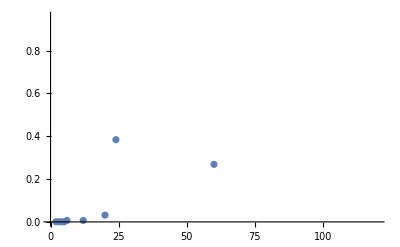

```mathematica
ListPlot[%]
```

## Bethe Vector

### Amplitude Function

```mathematica
Clear[d]
```

```mathematica
A[n_, d_, x_, s_]:= Signature[s]Product[(1 + x[s[[i]]]x[s[[j]]] - 2 d x[s[[i]]])/(1 + x[i] x[j]- 2 d x[i]), {i,1, n-1 }, {j, i+1, n}];
B[n_, d_, x_, s_]:= Signature[s]Product[1 + x[s[[i]]]x[s[[j]]] - 2 d x[s[[i]]], {i,1, n-1 }, {j, i+1, n}]Product[x[s[[k]]]^(k-1),{k, 1, n}];
```

```mathematica
A[2,d,  x, {2,1}]
B[2,d,  x, {2,1}]
```

-(1-2 d x[2]+x[1] x[2])/(1-2 d x[1]+x[1] x[2])

-x[1]^2 x[2] (1-2 d x[2]+x[1] x[2])

```mathematica
n =4;
sp = Permutations[Table[i, {i, 1, n}]][[RandomInteger[{1,n!}]]];
sub = Table[x[i]-> 1/x[i], {i, 1, n}];
A[n, d, x, sp]/.sub;
Simplify[A[n, d, x, sp](%)]
```

1

### Bethe coefficients

```mathematica
u[n_, d_, x_, xc_]:=Module[{per, i, j},
per = Permutations[Table[i, {i, 1, n}]];
Return[Sum[A[n, d, x, per[[j]]]Product[x[per[[j]][[i]]]^xc[i], {i, 1, n}], {j, 1, n!}]];
]
```

```mathematica
Clear[d]
u[2 , d, x, xc]
```

x[1]^xc[1] x[2]^xc[2]-(x[1]^xc[2] x[2]^xc[1] (1-2 d x[2]+x[1] x[2]))/(1-2 d x[1]+x[1] x[2])

### Bethe vector

```mathematica
Bv[n_, l_, d_, x_]:= Module[{conf, i,xc},
conf = Subsets[Table[i, {i, 1, l}], {n}];
Return[Table[u[n,d, x, xc]/.Sub[xc, conf[[i]]], {i, 1, Binomial[l, n]}]];
]
(*Transfer Matrix*)
TUM [n_, l_, d_]:= Module[{x, xc, br, conf, sub}, 
br= BR[n,l,d,x];
conf = Subsets[Table[i, {i, 1, l}], {n}];
sub = Table[Join[Sub[xc, conf[[j]]], br[[i]]], {i, 1, Binomial[l,n]}, {j, 1, Binomial[l,n]}];
Return[Chop[u[n, d,x, xc]/.sub]];
]
```

```mathematica
Umat =TUM[2, 3, 0];
MatrixForm[Umat]
```

(0.+1.73205 ⅈ | 1.5-0.866025 ⅈ | -1.5-0.866025 ⅈ
0.-1.73205 ⅈ | 1.5+0.866025 ⅈ | -1.5+0.866025 ⅈ
0.+1.73205 ⅈ | 0.+1.73205 ⅈ | 0.+1.73205 ⅈ)

```mathematica
Umat =TUM[2, 3, 0];
MatrixForm[Umat]
```

(0.+1.73205 ⅈ | 1.5-0.866025 ⅈ | -1.5-0.866025 ⅈ
0.-1.73205 ⅈ | 1.5+0.866025 ⅈ | -1.5+0.866025 ⅈ
0.+1.73205 ⅈ | 0.+1.73205 ⅈ | 0.+1.73205 ⅈ)

## Bethe Inverse

### Bethe Inverse Matrix Determinant

```mathematica
BIdet[x_, d_, n_, l_]:= Module[{mat, i, j},
mat= Table[If[i!=j,-(2d (1 + x[j]^2 - 2d x[j]))/((1 +x[i]x[j]-2d x[i] )(1 +x[i]x[j]-2d x[j] )), 0], {i, 1, n}, {j, 1, n}];
Do[mat[[i]][[i]]=l/x[i]-Sum[mat[[i]][[j]], {j, 1, n}], {i, 1, n}];
Return[Det[mat]];
]
```

```mathematica
Clear[d]
```

```mathematica
BIdet[x, 0, 2, 3]//MatrixForm
```

9/(x[1] x[2])

### ell-function

```mathematica
ell[yi_,x_ ,d_,  n_, l_]:=Module[{per, i, j},
per = Permutations[Table[i, {i, 1, n}]];
Return[(BIdet[x, d, n, l])^-1 Sum[(A[n, d, x, per[[i]]]Product[x[per[[i]][[j]]]^(yi[j]+1), {j, 1, n}])^-1, {i, 1, n!}]];
]
```

```mathematica
ell[yi, x, 0, 2, 3]
```

1/9 x[1] x[2] (-x[1]^(-1-yi[2]) x[2]^(-1-yi[1])+x[1]^(-1-yi[1]) x[2]^(-1-yi[2]))

### Transfer Ell Matrix

```mathematica
TLM[n_, l_, d_]:= Module[{br, conf, x, subs, i, j, len, yi},
br= BR[n,l,d,x];
conf = Subsets[Table[i, {i, 1, l}], {n}];
subs = Table[Join[Sub[yi, conf[[i]]], br[[j]]], {i, 1, Binomial[l,n]}, {j, 1,Binomial[l,n]}];
Return[Chop[ell[yi,x ,d,  n, l]/.subs]];
]
```

```mathematica
Lmat= TLM[2, 3, 0];
MatrixForm[Lmat]
```

(0.-0.19245 ⅈ | 0.+0.19245 ⅈ | 0.-0.19245 ⅈ
0.166667+0.096225 ⅈ | 0.166667-0.096225 ⅈ | 0.-0.19245 ⅈ
-0.166667+0.096225 ⅈ | -0.166667-0.096225 ⅈ | 0.-0.19245 ⅈ)

```mathematica
n=2;
l=3;
d=2.1;
Length[BR[n,l,d]]/Binomial[l,n]
Umat =TUM[n, l, d];
Lmat= TLM[n, l, d];
Chop[Umat.Lmat]//MatrixForm
Chop[Lmat.Umat]//MatrixForm
Clear[n, l, d];
```

1

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

## One Point Function

## Brute Force

### Energy

```mathematica
En[n_, d_,x_]:= Sum[x[i] + x[i]^-1-2 d, {i, 1, n}];
```

```mathematica
En[2, d, x]
```

-4 d+1/x[1]+x[1]+1/x[2]+x[2]

### One point configurations

```mathematica
OptConf[n_,l_, pt_]:=Module[{conf},
conf = Subsets[Table[i, {i, 1, l}], {n}];
Return[Select[conf,MemberQ[#, pt]& ]];
]
```

```mathematica
OptConf[2, 3, 1]
```

{{1,2},{1,3}}

### Fundamental Solution at time t

```mathematica
FunSol[n_, l_, d_, t_]:=Module[{br, x, bv, EN},
(*Bethe roots*)
br = BR[n, l, d,x];
(*Bethe vector*)
bv =Bv[n, l, d, x]/.br;
(*Energies*)
EN = Chop[En[n, d, x]/.br];
EN= Map[Exp[- I t #]&,EN ];
Return[Transpose[Inner[Times, EN, bv, List]]];
]
```

```mathematica
(*Set parameters*)
{n, l, d}={2, 3, 0.1};
(*Fundamental Solution*)
Fsol = Chop[FunSol[n, l, d, t]];
MatrixForm[Fsol]
(*Clear paramters*)
Clear[n,l, d]
```

((0.155+1.75385 ⅈ) ⅇ^((0.-1.8 ⅈ) t) | (0.155+1.75385 ⅈ) ⅇ^((0.-1.8 ⅈ) t) | (0.155+1.75385 ⅈ) ⅇ^((0.-1.8 ⅈ) t)
(-0.28+1.64973 ⅈ) ⅇ^((0.+1.2 ⅈ) t) | (1.56871-0.582377 ⅈ) ⅇ^((0.+1.2 ⅈ) t) | (-1.28871-1.06735 ⅈ) ⅇ^((0.+1.2 ⅈ) t)
(-0.28-1.64973 ⅈ) ⅇ^((0.+1.2 ⅈ) t) | (1.56871+0.582377 ⅈ) ⅇ^((0.+1.2 ⅈ) t) | (-1.28871+1.06735 ⅈ) ⅇ^((0.+1.2 ⅈ) t))

### IC solution

```mathematica
Lv[yi_,n_, l_, d_]:= Module[{br, i,x},
br=BR[n,l,d,x];
Return[{ell[yi,x ,d,  n, l]/.br}];
]
```

```mathematica
ICvec[yi_, n_, l_, d_]:= Module[{yitemp, sub},
sub= Sub[yitemp, yi];
Return[Lv[yitemp, n, l, d]/.sub]
]
```

```mathematica
{yi, n, l, d}= {{1,3}, 2, 3, 0.1};
IC = Chop[ICvec[yi, n,l, d]];
Clear[yi, n, l, d]
```

```mathematica
Chop[IC.Fsol/.t->0]
```

{{0,1.,0}}

### One-point function

```mathematica
OptConf[n_,l_, pt_]:=Module[{conf},
conf = Subsets[Table[i, {i, 1, l}], {n}];
Return[Select[conf,MemberQ[#, pt]& ]];
]
OptConfList[n_,l_, pt_]:=Module[{conf},
conf = Subsets[Table[i, {i, 1, l}], {n}];
Return[Table[If[MemberQ[conf[[i]], pt], 1, 0], {i,1,Binomial[l,n] }]];
]
OptSt[n_, l_,d_, pt_,yi_, t_]:=Module[{ptconfig, sol},
ptconfig =OptConfList[n, l,pt];
sol= Flatten[ICvec[yi, n,l, d].FunSol[n, l, d, t]];
Return[ Inner[Times, sol, ptconfig, List]];
] 
OptProb[n_, l_,d_, pt_,yi_, t_]:=Module[{temp},
Return[Norm[OptSt[n, l,d, pt,yi, temp]/.temp->t]^2];
]
```

```mathematica
ptconfig =OptConfList[2, 3,2]
```

{1,0,1}

```mathematica
{n, l, dtemp, pt}= {2, 21,.13, 2};
dtemp
Length[BR[n, l, dtemp]]/Binomial[l,n]
Clear[n, l, d, pt, yi]
```

0.13

1

```mathematica
{n, l, d, yi}= {2, 21, 0.13, {7,14}};
times= Table[dt, {dt, 0, l/2, 0.1}];
lentimes = Length[times];
MasProbs={};
Do[ 
optst =OptSt[n, l ,d, pt, yi, t];
tsub =Table[{t->times[[k]]}, {k, 1, lentimes}];
probs =Map[ Norm[#]^2&,optst/.tsub];
probs =Table[{pt, times[[k]], probs[[k]]}, {k, 1, lentimes}];
MasProbs = Join[MasProbs, probs],
{pt, 1, l}
]
Clear[n, l, d, pt, yi]
```

-Graphics3D-

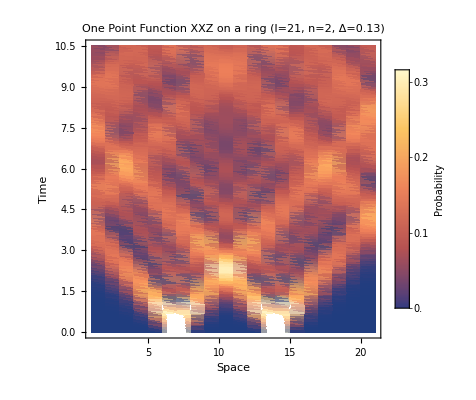

```mathematica
ListPlot3D[MasProbs, PlotRange->Full,PlotLabel->Style["One Point Function XXZ on a ring (l=21, n=2, Δ=0.13)", Bold, Black], AxesLabel->{Style["Space",Black], Style["Time", Black], Style["Probability", Black]}]
ListDensityPlot[MasProbs,PlotLabel->Style["One Point Function XXZ on a ring (l=21, n=2, Δ=0.13)", Bold, Black],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Probability",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right], Frame-> True, FrameLabel->{Style["Space", Black],Style["Time", Black]}]
```

```mathematica
ListPlot3D[MasProbs, PlotRange->Full,PlotLabel->Style["One Point Function XXZ on a ring (l=21, n=2, Δ=0)", Bold, Black], AxesLabel->{Style["Space",Black], Style["Time", Black], Style["Probability", Black]}]
```

-Graphics3D-

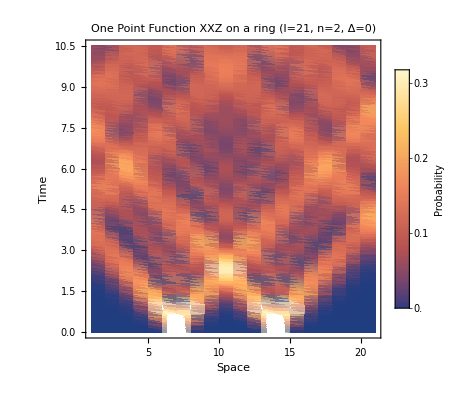

```mathematica
ListDensityPlot[MasProbs,PlotLabel->Style["One Point Function XXZ on a ring (l=21, n=2, Δ=0)", Bold, Black],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Probability",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right], Frame-> True, FrameLabel->{Style["Space", Black],Style["Time", Black]}]
```

```mathematica
Clear[MasProb, MasProbs]
```

## Alternate by Idenities

```mathematica
(*
`ρ(x, t)= One point function
=Subscript[Σ, ξ,ϛ∈BetheRoots] l(y, ξ)l(y, ζ)(Subscript[Σ, s=1]^N LHS1)(Subscript[Π, 1 <=i<j<=n](1 + Subscript[ξ, i] Subscript[ξ, j] -2 Subscript[Δξ, i] )(1+Subscript[ϛ, i] Subscript[ϛ, j]-2 Subscript[Δϛ, i]))^-1 e^(-i t (E(ξ)-E(ϛ)))
*)
```

```mathematica
OptAlt[n_, l_, d_,pt_, yi_, t_]:= Module[{yit, ysub, brx, brz,br,ans, s, i, j, x, z},
yi= Sort[Mod[yi-pt-1, l] +1];
ysub =Sub[yit, yi];
br = BR[n, l, d];
brx = Map[Sub[x, #]&, br];
brz = Map[Sub[z, #]&, br];
ans = ell[yit,x ,d,  n, l]ell[yit,z ,d,  n, l]Sum[LHS1[n, s, d, x, z], {s, 1, n}]Product[(1 + x[i] x[j]- 2 d x[i])^-1(1 + z[i]z[j]- 2d z[i])^-1, {i, 1, n-1}, {j, i+1, n}]Exp[- I t(En[n, d, x]- En[n, d, z])]/.ysub;
Print[ans];
ans = Flatten[ans/. brx/.brz];
j = Length[ans];
Return[Sum[ans[[i]], {i, 1, j}]];
]
```

```mathematica
{n, l, d, yi, pt} = {2, 3, 0, {1, 2}, 1};
yi= Sort[Mod[yi-pt-1, l] +1];
ysub =Sub[yit, yi];
br = BR[n, l, d];
brx = Map[Sub[x, #]&, br];
brz = Map[Sub[z, #]&, br];
ans = ell[yit,x ,d,  n, l]ell[yit,z ,d,  n, l]Sum[LHS1[n, s, d, x, z], {s, 1, n}]Product[(1 + x[i] x[j]- 2 d x[i])^-1(1 + z[i]z[j]- 2d z[i])^-1, {i, 1, n-1}, {j, i+1, n}]Exp[- I t(En[n, d, x]- En[n, d, z])]/.ysub/.t->0;
FullSimplify[ans]
Simplify[Together[LHS1[n, 1, d, x, z]]]
(*Table[OptAlt[n, l, d,pt, yi, 0], {pt, 1, n}]*)
Clear[n, l, d, yi, br, brx, brz, ans, pt]
```

((x[1]^2-x[2]^2) (z[1]^2-z[2]^2) (x[1] (-2 x[2] z[2] (x[2]+z[2])-2 x[2] z[1]^2 z[2] (x[2]+z[2])-z[1] (-1-x[2]+(-1+x[2]) z[2]) (1+x[2] z[2]) (-1+x[2]+z[2]+x[2] z[2]))+x[2] z[2] (1+z[1]^2-2 z[1] z[2]+x[2] (z[2]+z[1] (-2+z[1] z[2])))+x[1]^2 x[2] z[2] (1+z[1]^2-2 z[1] z[2]+x[2] (z[2]+z[1] (-2+z[1] z[2])))))/(81 x[1]^4 x[2]^4 (x[2]-z[1]) z[1]^4 (-1+x[2] z[1]) (x[1]-z[2]) z[2]^4 (-1+x[1] z[2]) (-1+x[2] z[2]))

((-1+x[1] x[2]) (1+x[1] x[2]) (x[1] z[1]-x[2] z[2]) (-1+z[1] z[2]) (1+z[1] z[2]))/(x[1] x[2] (x[2]-z[1]) z[1] (-1+x[1] z[1]) (x[1]-z[2]) z[2] (-1+x[2] z[2]))

```mathematica
(1 -F[x,z, {1}, {1}])F[x, z, {2}, {2}]^-1 Λ[d, x, z, {1}, {1}]G[d, x, {{2}, {1}}, {1,2}]G[d, z, {{2}, {1}}, {1,2}]Λi[d, x, z, {2}, {2}]
Simplify[(1 -F[x,z, {1}, {2}])F[x, z, {2}, {1}]^-1 Λ[d, x, z, {1}, {2}]G[d, x, {{2}, {1}}, {1,2}]G[d, z, {{1}, {2}}, {1,2}]Λi[d, x, z, {2}, {1}]]
```

((-1+2 d x[2]-x[1] x[2]) (-1+2 d z[2]-z[1] z[2]))/(x[2] z[2] (1-x[2] z[2]))

((-1+2 d x[2]-x[1] x[2]) (-1+2 d z[1]-z[1] z[2]))/(x[2] (x[2]-z[1]))

```mathematica
F[x,z, {1}, {2}]
G[d, x, {{1}, {2}}, {1,2}]
```

x[1] z[2]

1-2 d x[1]+x[1] x[2]

```mathematica
Factor[Together[Λ[d, x, z, {1}, {1}]]]
Factor[Together[Λi[d, x, z, {1}, {1}]]]
```

-1/(-1+x[1] z[1])

(x[1] z[1])/(-1+x[1] z[1])

## Checking One Point Functions

### Master sum

The master sum is

Σ_(x_1=0)Σ_(σ,μ ∈S_N)B_σ(ξ)B_μ(ϛ)(Π_(j=1))^N(ξ_(σ(j)))^(x_j-j)(ϛ_(μ(j)))^(x_j-j)

```mathematica
MasterSum[x_, z_, d_, n_, l_]:=Module[{per,i, j, k, len, ans, confs, xc},
per = Permutations[Table[i, {i, 1, n}]];
confs= Map[Sub[xc, #]&,OptConf[n, l, 1]-1];
len= Length[confs];
ans =Sum[B[n, d, x, per[[i]]]B[n, d,z, per[[j]]]Product[x[per[[i]][[k]]]^(xc[k]-k)z[per[[j]][[k]]]^(xc[k]-k), {k, 1, n}], {i, 1, n!}, {j, 1, n!}];
ans = ans/.confs;
Return[Sum[ans[[k]], {k, 1, len}]]
]
```

```mathematica
ans =Simplify[MasterSum[x, z, d, 2, 3]]
Clear[ans]
```

(x[1] (1-2 d x[2]+x[1] x[2]) z[2] (-1+2 d z[1]-z[1] z[2])+x[1]^2 (1-2 d x[2]+x[1] x[2]) z[2]^2 (-1+2 d z[1]-z[1] z[2])+x[2] (1-2 d x[1]+x[1] x[2]) z[1] (-1+2 d z[2]-z[1] z[2])+x[2]^2 (1-2 d x[1]+x[1] x[2]) z[1]^2 (-1+2 d z[2]-z[1] z[2])+x[2] (1-2 d x[1]+x[1] x[2]) z[2] (1-2 d z[1]+z[1] z[2])+x[2]^2 (1-2 d x[1]+x[1] x[2]) z[2]^2 (1-2 d z[1]+z[1] z[2])+x[1] (1-2 d x[2]+x[1] x[2]) z[1] (1-2 d z[2]+z[1] z[2])+x[1]^2 (1-2 d x[2]+x[1] x[2]) z[1]^2 (1-2 d z[2]+z[1] z[2]))/(x[1] x[2] z[1] z[2])

```mathematica
Map[Sub[xc, #]&, OptConf[2,3, 1]-1]
```

{{xc[1]→0,xc[2]→1},{xc[1]→0,xc[2]→2}}

### Sum over configurations

Gonna code the identity

```mathematica
F1[x_, indexset_]:= Product[x[indexset[[k]]], {k, 1, Length[indexset]}];
```

```mathematica
F1[x, {}]
```

1

```mathematica
Id1Term[n_, l_, x_, Iset_]:= Module[{len, set, ans},
len = Length[Iset];
set = Join[{1}, Iset];
set = Join[set, {n+1}];
ans = (-1)^len((1 - F1[x, Table[i, {i, set[[1]], set[[2]]-1}]])/F1[x, Table[i, {i, set[[1]], set[[2]]-1}]])(F1[x, If[set[[2]]<= n, Table[i, {i, set[[2]],n}], {}]])^(l-n)Product[Product[(1- F1[x,Table[k, {k, j, set[[i+1]]-1}] ])^-1, {j, set[[i]], set[[i+1]]-1}], {i,1,len+1 }];
Return[ans]
]
```

```mathematica
Simplify[Id1Term[2, 3, x, {}]+Id1Term[2, 3, x, {2}]]
```

(1+x[2])/(x[1] x[2])

```mathematica
Id1[n_, l_,x_]:=Module[{subindex, len, i},
subindex= Subsets[Table[i, {i, 2, n}], n-1];
len = Length[subindex];
subindex=Map[Id1Term[n, l, x, #]&, subindex];
Return[Sum[subindex[[i]], {i, 1, len}]];
]
```

```mathematica
Simplify[Id1[2, 3, x]]
```

(1+x[2])/(x[1] x[2])

```mathematica
GeoSum[n_, l_, x_]:= Module[{confs, ans, xc, len, i, j},
confs= Map[Sub[xc, #]&,OptConf[n, l, 1]-1];
len = Length[confs];
ans = Product[x[j]^(xc[j]-j), {j, 1, n}];
ans= ans/.confs;
Return[Sum[ans[[i]], {i, 1, len}]]
]
```

```mathematica
Simplify[GeoSum[2, 3, x]]
```

(1+x[2])/(x[1] x[2])

```mathematica
{n, l}= {5,6};
Simplify[Id1[n, l, x]- GeoSum[n, l, x]]
Clear[n, l]
```

0

### C-function

```mathematica
CsTerm[n_, l_, x_, z_, per1_, per2_, Iset_]:= Module[{len, set, ans},
len = Length[Iset];
set = Join[{1}, Iset];
set = Join[set, {n+1}];
ans = ((1 - F[x, z, Table[per1[[i]], {i, set[[1]], set[[2]]-1}], Table[per2[[i]], {i, set[[1]], set[[2]]-1}]])/F[x, z, Table[per1[[i]], {i, set[[1]], set[[2]]-1}], Table[per2[[i]], {i, set[[1]], set[[2]]-1}]])(F[x, z, If[set[[2]]<= n, Table[per1[[i]], {i, set[[2]],n}], {}], If[set[[2]]<= n, Table[per2[[i]], {i, set[[2]],n}], {}]])^(l-n)Product[Product[(1- F[x,z, Table[per1[[k]], {k, j, set[[i+1]]-1}], Table[per2[[k]], {k, j, set[[i+1]]-1}] ])^-1, {j, set[[i]], set[[i+1]]-1}], {i,1,len+1 }];
Return[ans]
]
```

```mathematica
CsTerm[2,3, x, z, {2, 1}, {1,2}, {}]
```

1/(x[1] x[2] z[1] z[2] (1-x[1] z[2]))

```mathematica
Cs[n_, l_, d_, x_, z_, Iset_]:= Module[{perms, i, j, ans, len},
perms = Permutations[Table[i, {i, 1, n}]];
ans = Flatten[Table[B[n, d, x, perms[[i]]]B[n, d,z, perms[[j]]]CsTerm[n, l, x, z, perms[[i]], perms[[j]], Iset], {i, 1, n!}, {j, 1, n!}]];
len = Length[ans];
Return[Sum[ans[[i]], {i,1 ,len}]]
]
```

```mathematica
ans =Simplify[MasterSum[x, z, d, 2, 3]-Cs[2, 3, d, x, z, {}]+Cs[2, 3, d, x, z, {2}]]
Clear[ans]
```

0

```mathematica
CsSum[n_, l_, d_,x_, z_]:=Module[{subindex, len, i},
subindex= Subsets[Table[i, {i, 2, n}], n-1];
len = Length[subindex];
subindex=Map[(-1)^Length[#] Cs[n, l, d, x, z, #]&, subindex];
Return[Sum[subindex[[i]], {i, 1, len}]];
]
```

```mathematica
{n, l}={3, 5};
Simplify[MasterSum[x, z, d, n, l]-
CsSum[n, l, d, x, z]]
Clear[n, l]
```

0

### C-function decomposition

```mathematica
Ecs[x_, z_, d_, I1_, I2_]:= ( F[x, z, I1, I2]^-1-1)Λ[d, x,z, I1, I2 ];
```

```mathematica
DsTerm[n_, l_, x_, z_, per1_, per2_, Iset_, I1c_, I2c_]:= Module[{len, set, ans, len2},
len = Length[Iset];
len2 = Length[I1c];
set = Join[{1}, Iset];
set = Join[set, {n+1}];
ans = Product[(F[x, z, Table[I1c[[per1[[k + len2-n]]]], {k, set[[i]], set[[i+1]]-1}], Table[I2c[[per2[[k + len2-n]]]], {k, set[[i]], set[[i+1]]-1}] ])^(l-len2)Product[(1- F[x,z, Table[I1c[[per1[[k+len2-n]]]], {k, j, set[[i+1]]-1}], Table[I2c[[per2[[k+len2-n]]]], {k, j, set[[i+1]]-1}] ])^-1, {j, set[[i]], set[[i+1]]-1}], {i,2,len+1 }];
Return[ans]
]
B[n_, d_, x_, perm_, Ic_]:= Module[{len, sub, i},
len = Length[Ic];
sub =Table[x[i]-> x[Ic[[i]]], {i, 1, len}];
Return[B[len, d, x, perm]/.sub]
]
Ds[n_, l_, d_, x_, z_, Iset_, I1c_, I2c_]:= Module[{perms, i, j, ans, len},
If[Length[I1c]==0, Return[1]];
perms = Permutations[Table[i, {i, 1, n- Iset[[1]]+1}]];
ans = Flatten[Table[B[n, d, x, perms[[i]], I1c]B[n, d,z, perms[[j]], I2c]DsTerm[n, l, x, z, perms[[i]], perms[[j]], Iset, I1c, I2c], {i, 1, (n- Iset[[1]]+1)!}, {j, 1, (n- Iset[[1]]+1)!}]];
len = Length[ans];
Return[Sum[ans[[i]], {i,1 ,len}]]
]
```

```mathematica
DsTerm[2, 3, x, z,{1}, {1}, {2}, {2}, {2} ]
```

(x[2]^2 z[2]^2)/(1-x[2] z[2])

```mathematica
Ds[2, 3, x, z,{1}, {1}, {2}, {2}, {2} ]
```

```mathematica
B[2,3, x, {1}, {2}]
```

1

```mathematica
Ds[2,3, d, x, z, {2}, {2}, {2}]
```

(x[2]^2 z[2]^2)/(1-x[2] z[2])

```mathematica
CsRHS[n_, l_, d_, x_, z_, Iset_]:= Module[{s1, sets, i,j, len, supset},
If[Length[Iset]==0, s1= n+1, s1 = Iset[[1]]];
supset=Table[i, {i, 1, n}];
sets = Subsets[supset, {s1-1}];
len = Length[sets];
Return[Sum[Ecs[x, z, d, sets[[i]], sets[[j]]]G[d, x,{sets[[i]], Complement[supset, sets[[i]]]}, {1,2} ]G[d, z,{sets[[j]], Complement[supset, sets[[j]]]} , {1,2}]Ds[n, l, d, x, z, Iset, Complement[supset, sets[[i]]],Complement[supset, sets[[j]]]], {i, 1, len}, {j, 1, len}]];
]
```

```mathematica
{n, l}={2, 3};
Ecs[x, z, d, {1,2}, {1,2}];
G[d,x, {{1,2}, {}}, {1,2}];
Ds[n, l,d, x, z, {}, {}, {} ]
Clear[n,l]
```

1

```mathematica
CsRHS[2, 3, d, x, z, {}]//Simplify
```

-(((x[1]-x[2]) (z[1]-z[2]) (-1+x[1] x[2] z[1] z[2]) (1+(1-2 d x[2]) z[1] z[2]+x[1] (-2 d z[1] z[2]+x[2] (1+z[1] z[2]+4 d^2 z[1] z[2]-2 d (z[1]+z[2])))))/(x[1] x[2] z[1] (-1+x[1] z[1]) (-1+x[2] z[1]) z[2] (-1+x[1] z[2]) (-1+x[2] z[2])))

```mathematica
Simplify[Cs[2, 3, d, x, z, {2}]- CsRHS[2, 3, d, x, z, {2}]]
```

0

```mathematica
CsSumRHS[n_, l_, d_,x_, z_]:=Module[{subindex, len, i},
subindex= Subsets[Table[i, {i, 2, n}], n-1];
len = Length[subindex];
subindex=Map[(-1)^Length[#] CsRHS[n, l, d, x, z, #]&, subindex];
Return[Sum[subindex[[i]], {i, 1, len}]];
]
```

```mathematica
{n, l}={3, 5};
Simplify[
CsSum[n, l, d, x, z]-CsSumRHS[n, l, d, x, z]]
Clear[n, l]
```

0

```mathematica
{n, l}={2, 3};
Simplify[
MasterSum[x, z, d, n, l]-CsSumRHS[n, l, d, x, z]]
Clear[n, l]
```

0

### Lemma B-decomposition

```mathematica
B[n_, d_, x_, perm_, Ic_]
```

```mathematica
{n,s}= {6,3};
per = Permutations[Table[i, {i, 1, n}]][[RandomInteger[n]+1]]
I1per= Table[per[[i]], {i, 1, s}];
I1 =Sort[I1per];
I1cper= Table[per[[i]], {i, s+1, n}];
I1c = Sort[I1cper];
B[s, d, x, I1per];
B[n-s, d, x, I1cper];
B[n, d, x, per];
Simplify[B[n, d, x, per]/(B[s, d, x, I1per]G[d, x, {I1, I1c}, {1,2}]B[n-s, d, x, I1cper] F1[x,I1c ]^Length[I1])]
Clear[n, per, I1, I1per, I1c, I1cper, s]
```

{1,2,3,5,4,6}

1

### Ds Identity

```mathematica
DsSumLHS[n_, l_, d_,x_, z_, s_, I1c_, I2c_]:=Module[{subindex, len, i},
subindex= Subsets[Table[i, {i, s+2, n}], n-2];
subindex = Map[Join[{s+1}, #]&, subindex];
len = Length[subindex];
subindex=Map[(-1)^Length[#] Ds[n, l, d, x, z, #, I1c, I2c]&, subindex];
Return[Sum[subindex[[i]], {i, 1, len}]];
]
```

```mathematica
{n,l , s}= {3,4, 1};
I1c = {1,2};
I2c ={1,2};
Simplify[DsSumLHS[n, l, d, x, z, s, I1c, I2c]/(Λi[d, x, z, I1c, I2c] F[x, z,I1c, I2c ]^(l+n-(s+1)-2))]
l+n-(s+1)-2
Clear[n, l, s, I1c, I2c]
```

1

3

```mathematica
DsSumId[n_, l_ ,d_, x_, z_,s_, I1c_, I2c_ ]:=Λi[d, x, z, I1c, I2c] F[x, z,I1c, I2c ]^(l+n-(s+1)-2);
```

#### Ds identity sum

```mathematica
F[x, z, {}, {}]
```

1

```mathematica
DsSumMaster[n_, l_, d_,x_, z_] := Module[{supset, sets, i, len, s}, 
supset = Table[i, {i, 1, n}];
sets = Subsets[supset];
len = Length[sets];
Return[Sum[Ecs[x, z, d, sets[[i]], sets[[j]]]G[d, x, { sets[[i]],Complement[supset, sets[[i]]]}, {1,2}]G[d, z, { sets[[j]],Complement[supset, sets[[j]]]}, {1,2}]DsSumId[n, l ,d, x, z,Length[sets[[i]]], Complement[supset, sets[[i]]], Complement[supset, sets[[j]]] ], {i, 1, len}, {j, 1, len}]];
]
```

```mathematica
{n ,l}= {2, 3};
Simplify[DsSumMaster[n, l, d, x, z] -MasterSum[x, z, d, n, l] ]
Clear[n, l]
```

0

```mathematica
Simplify[Λ[d, x, z, {1}, {2}]/.x[1]->1/x[1]/.z[2]->1/z[2]]
```

(x[1] z[2])/(-1+x[1] z[2])

## Misc

```mathematica
n =2;
per= Permutations[Table[i, {i, 1, n}]];
ans5 = Sum[B[n, d, x, per[[i]]] B[n, d, z, per[[j]]]/Product[1 - Product[x[per[[i]][[k]]] z[per[[j]][[k]]], {k, i1, n}], {i1, 1, n}], {i, 1, n!}, {j, 1, n!}];
ans5 = Together[ans5];
```

```mathematica
Denominator[ans5]
```

(-1+x[1] z[1]) (-1+x[2] z[1]) (-1+x[1] z[2]) (-1+x[2] z[2])

```mathematica
Clear[d]
```

```mathematica
SeriesCoefficient[Numerator[ans5]/((x[2]-x[1])(z[2]-z[1])), {d, 0, 2}]
SeriesCoefficient[Numerator[ans5]/((x[2]-x[1])(z[2]-z[1])), {d, 0, 1}]
SeriesCoefficient[Numerator[ans5]/((x[2]-x[1])(z[2]-z[1])), {d, 0, 0}]
```

4 x[1] x[2] z[1] z[2]

-2 (x[1] x[2] z[1]+x[1] x[2] z[2]+x[1] z[1] z[2]+x[2] z[1] z[2])

1+x[1] x[2]+z[1] z[2]+x[1] x[2] z[1] z[2]

```mathematica
Van[n_, x_]:= Product[x[j]-x[i], {i, 1, n-1}, {j, i+1, n}];
```

```mathematica
n =2;
per= Permutations[Table[i, {i, 1, n}]];
ans6 = Sum[B[n, d, x, per[[i]]] B[n, d, z, per[[j]]], {i, 1, n!}, {j, 1, n!}];
ans6 = Together[ans6];
Factor[ans6/(Van[n, x]Van[n,z])]
```

(1+x[1] x[2]) (1+z[1] z[2])

```mathematica
n =6;
per= Permutations[Table[i, {i, 1, n}]];
ans7= Sum[B[n, d, x, per[[i]]] , {i, 1, n!}];
ans7 = Together[ans7];
Factor[ans7/Van[n,x]];
Length[%]
n!Binomial[n,2]
```

13510

10800

```mathematica
N[859/1200]
```

0.715833

```mathematica
Length[%]
```

72

```mathematica
n!Binomial[n,2]
```

144